# Sec 3

## Sec 3.1 -- Asymptotic Solution

## Multi-Leading Term Cancellation

```mathematica
eqaBeta=36 (α-γ) η^4 a[r]^4+3 r η^3 a[r]^3 (24 (-α+γ) η-4 (β+5 γ-2 (β+2 γ) η+α (-5+4 η)) a'[r]+r (β+8 γ+4 α (-2+η)-5 β η-4 γ η) a''[r]+r^2 β ((1+η) Derivative[3][a][r]+r (-2+η) Derivative[4][a][r]))+r^4 (η (8 γ (-2+η) (-1+η)+3 β (1+η) (-4+3 η)) a'[r]^3-(-2+η) (γ (-2+η)+3 β η (1+η)) a'[r]^4+η a'[r]^2 (η (-3 r^2 (-2+η)-16 γ (-1+η)^2+6 η (β+2 α (-2+η)-2 β η))-r (-2+η) (2 γ (-2+η)+β (6+9 η)) a''[r])+η^2 a'[r] (-6 (r^2+2 β) (-1+η) η+r (8 γ (-2+η) (-1+η)+3 β (-8+η (6+η))) a''[r]+3 r^2 β (-3+η) (-2+η) Derivative[3][a][r])-r η^2 (3 (r^2 (-2+η)-4 β (-1+η)) η a''[r]+r (6 β+γ (-2+η)) (-2+η) a''[r]^2+3 r β η (2 (-1+η) Derivative[3][a][r]+r (-2+η) Derivative[4][a][r])))+r^2 η^2 a[r]^2 (36 (α-γ) η^2+(12 α (-2+η) (-1+η)+3 β (5-4 η) η+γ (-49+4 (13-4 η) η)) a'[r]^2+a'[r] (3 η (r^2-36 α+11 β+36 γ-2 (r^2-16 α+10 β+16 γ) η)+r (2 γ (-2+η) (-5+4 η)+3 β (-5+η (2+η))) a''[r]+3 r^2 β (-3+η) (-2+η) Derivative[3][a][r])+r (-3 η (5 β+16 γ+r^2 (-2+η)+8 α (-2+η)-14 β η-8 γ η) a''[r]-r (6 β+γ (-2+η)) (-2+η) a''[r]^2-3 r β η (4 η Derivative[3][a][r]+3 r (-2+η) Derivative[4][a][r])))+r^3 η a[r] (-((-2+η) (3 β+2 γ (-5+4 η)) a'[r]^3)+a'[r]^2 (η (-24 α+3 β+64 γ+3 r^2 (-2+η)+2 η (6 α (5-2 η)+3 β (-5+4 η)+2 γ (-21+8 η)))+r (-2+η) (2 γ (-2+η)+β (6+9 η)) a''[r])-η a'[r] (3 r^2 (3-4 η) η+6 η (5 β+8 γ+8 α (-1+η)-8 (β+γ) η)+r (-39 β+6 β η (4+η)+2 γ (-2+η) (-9+8 η)) a''[r]+6 r^2 β (-3+η) (-2+η) Derivative[3][a][r])+r η (3 η (-8 α+8 (β+γ)+2 r^2 (-2+η)+4 α η-13 β η-4 γ η) a''[r]+2 r (6 β+γ (-2+η)) (-2+η) a''[r]^2+3 r β η ((-3+5 η) Derivative[3][a][r]+3 r (-2+η) Derivative[4][a][r])));
```

#### Ansatz

[Note: The naming cnkm denotes r^{n*k+m} ]

With the ansatz, we can pick out terms with potentially the largest power.

```mathematica
a[r_]:=r^k
```

```mathematica
eqaBeta//FullSimplify
```

r^k (36 r^k (r-r^k)^2 (α-γ) η^4+k^4 (-2+η) (r^(1+2 k) (β (6-15 η)+2 γ (-2+η)) (-1+η) η-3 r^3 β η^3-r^(3 k) (-1+η) (γ (-2+η) (-1+η)+3 β (1-2 η) η)+r^(2+k) η^2 (-γ (-2+η)+3 β (-5+4 η)))+3 k η^3 (-r^3 (r^2+6 β) η+r^(2+k) (r^2+12 (2 α+β-2 γ)+(2 r^2-20 α+21 β+20 γ) η)-r^(1+2 k) (52 α+20 β-52 γ+8 (-5 α+3 β+5 γ) η+r^2 (1+η))+r^(3 k) (4 α (7-5 η)+9 β (1+η)+4 γ (-7+5 η)))+k^2 η^2 (-3 r^3 (β (-12+η)+r^2 (-2+η)) η-r^(1+2 k) (12 (11 β-9 γ)+3 r^2 (-2+η) (-1+η)+2 γ (95-37 η) η+3 β (-83+η) η+12 α (-2+η) (-1+4 η))+r^(3 k) (β (63-99 η)+12 α (-2+η) (-1+2 η)+γ (-73+(106-37 η) η))+r^(2+k) (72 β-36 γ+3 r^2 (-2+η) (-1+2 η)+η (γ (84-37 η)+24 α (-2+η)+3 β (-65+2 η))))+k^3 η (6 r^3 β η^2 (-5+2 η)-r^(2+k) η (-2 γ (-2+η) (-6+5 η)+3 β (34+η (-58+15 η)))+r^(3 k) (2 γ (-2+η) (-1+η) (-7+5 η)+3 β (6+η (-28+(31-7 η) η)))+2 r^(1+2 k) (-2 γ (-2+η) (3+η (-9+5 η))+3 β (-4+η (30+η (-38+9 η))))))

```mathematica
Leadings=Series[eqaBeta,{r,Infinity,10}]//Normal//Expand
```

-4 k^4 r^(4 k) γ+18 k^3 r^(4 k) β η-6 k^4 r^(4 k) β η-24 k^3 r^(1+3 k) β η+12 k^4 r^(1+3 k) β η-28 k^3 r^(4 k) γ η+12 k^4 r^(4 k) γ η+24 k^3 r^(1+3 k) γ η-8 k^4 r^(1+3 k) γ η+6 k^2 r^(4+2 k) η^2-6 k^2 r^(3+3 k) η^2+24 k^2 r^(4 k) α η^2-24 k^2 r^(1+3 k) α η^2+63 k^2 r^(4 k) β η^2-84 k^3 r^(4 k) β η^2+21 k^4 r^(4 k) β η^2+72 k^2 r^(2+2 k) β η^2-102 k^3 r^(2+2 k) β η^2+30 k^4 r^(2+2 k) β η^2-132 k^2 r^(1+3 k) β η^2+180 k^3 r^(1+3 k) β η^2-48 k^4 r^(1+3 k) β η^2-73 k^2 r^(4 k) γ η^2+62 k^3 r^(4 k) γ η^2-13 k^4 r^(4 k) γ η^2-36 k^2 r^(2+2 k) γ η^2+24 k^3 r^(2+2 k) γ η^2-4 k^4 r^(2+2 k) γ η^2+108 k^2 r^(1+3 k) γ η^2-84 k^3 r^(1+3 k) γ η^2+16 k^4 r^(1+3 k) γ η^2+6 k^2 r^(5+k) η^3+3 k r^(4+2 k) η^3-15 k^2 r^(4+2 k) η^3-3 k r^(3+3 k) η^3+9 k^2 r^(3+3 k) η^3+84 k r^(4 k) α η^3-60 k^2 r^(4 k) α η^3+72 k r^(2+2 k) α η^3-48 k^2 r^(2+2 k) α η^3-156 k r^(1+3 k) α η^3+108 k^2 r^(1+3 k) α η^3+27 k r^(4 k) β η^3-99 k^2 r^(4 k) β η^3+93 k^3 r^(4 k) β η^3-21 k^4 r^(4 k) β η^3+36 k^2 r^(3+k) β η^3-30 k^3 r^(3+k) β η^3+6 k^4 r^(3+k) β η^3+36 k r^(2+2 k) β η^3-195 k^2 r^(2+2 k) β η^3+174 k^3 r^(2+2 k) β η^3-39 k^4 r^(2+2 k) β η^3-60 k r^(1+3 k) β η^3+249 k^2 r^(1+3 k) β η^3-228 k^3 r^(1+3 k) β η^3+51 k^4 r^(1+3 k) β η^3-84 k r^(4 k) γ η^3+106 k^2 r^(4 k) γ η^3-44 k^3 r^(4 k) γ η^3+6 k^4 r^(4 k) γ η^3-72 k r^(2+2 k) γ η^3+84 k^2 r^(2+2 k) γ η^3-32 k^3 r^(2+2 k) γ η^3+4 k^4 r^(2+2 k) γ η^3+156 k r^(1+3 k) γ η^3-190 k^2 r^(1+3 k) γ η^3+76 k^3 r^(1+3 k) γ η^3-10 k^4 r^(1+3 k) γ η^3-3 k r^(5+k) η^4-3 k^2 r^(5+k) η^4+6 k r^(4+2 k) η^4+6 k^2 r^(4+2 k) η^4-3 k r^(3+3 k) η^4-3 k^2 r^(3+3 k) η^4+36 r^(4 k) α η^4-60 k r^(4 k) α η^4+24 k^2 r^(4 k) α η^4+36 r^(2+2 k) α η^4-60 k r^(2+2 k) α η^4+24 k^2 r^(2+2 k) α η^4-72 r^(1+3 k) α η^4+120 k r^(1+3 k) α η^4-48 k^2 r^(1+3 k) α η^4+27 k r^(4 k) β η^4-21 k^3 r^(4 k) β η^4+6 k^4 r^(4 k) β η^4-18 k r^(3+k) β η^4-3 k^2 r^(3+k) β η^4+12 k^3 r^(3+k) β η^4-3 k^4 r^(3+k) β η^4+63 k r^(2+2 k) β η^4+6 k^2 r^(2+2 k) β η^4-45 k^3 r^(2+2 k) β η^4+12 k^4 r^(2+2 k) β η^4-72 k r^(1+3 k) β η^4-3 k^2 r^(1+3 k) β η^4+54 k^3 r^(1+3 k) β η^4-15 k^4 r^(1+3 k) β η^4-36 r^(4 k) γ η^4+60 k r^(4 k) γ η^4-37 k^2 r^(4 k) γ η^4+10 k^3 r^(4 k) γ η^4-k^4 r^(4 k) γ η^4-36 r^(2+2 k) γ η^4+60 k r^(2+2 k) γ η^4-37 k^2 r^(2+2 k) γ η^4+10 k^3 r^(2+2 k) γ η^4-k^4 r^(2+2 k) γ η^4+72 r^(1+3 k) γ η^4-120 k r^(1+3 k) γ η^4+74 k^2 r^(1+3 k) γ η^4-20 k^3 r^(1+3 k) γ η^4+2 k^4 r^(1+3 k) γ η^4

```mathematica
c4k2=Coefficient[Leadings,r^(4 k+2)]
c4k1=Coefficient[Leadings,r^(4 k+1)]
c4k0=Coefficient[Leadings,r^(4 k)]//FullSimplify
Leadings=Leadings-c4k0*r^(4k)//Expand
```

0

0

36 (α-γ) η^4-k^4 (-2+η) (-1+η) (γ (-2+η) (-1+η)+3 β (1-2 η) η)+3 k η^3 (4 α (7-5 η)+9 β (1+η)+4 γ (-7+5 η))+k^2 η^2 (β (63-99 η)+12 α (-2+η) (-1+2 η)+γ (-73+(106-37 η) η))+k^3 η (2 γ (-2+η) (-1+η) (-7+5 η)+3 β (6+η (-28+(31-7 η) η)))

-24 k^3 r^(1+3 k) β η+12 k^4 r^(1+3 k) β η+24 k^3 r^(1+3 k) γ η-8 k^4 r^(1+3 k) γ η+6 k^2 r^(4+2 k) η^2-6 k^2 r^(3+3 k) η^2-24 k^2 r^(1+3 k) α η^2+72 k^2 r^(2+2 k) β η^2-102 k^3 r^(2+2 k) β η^2+30 k^4 r^(2+2 k) β η^2-132 k^2 r^(1+3 k) β η^2+180 k^3 r^(1+3 k) β η^2-48 k^4 r^(1+3 k) β η^2-36 k^2 r^(2+2 k) γ η^2+24 k^3 r^(2+2 k) γ η^2-4 k^4 r^(2+2 k) γ η^2+108 k^2 r^(1+3 k) γ η^2-84 k^3 r^(1+3 k) γ η^2+16 k^4 r^(1+3 k) γ η^2+6 k^2 r^(5+k) η^3+3 k r^(4+2 k) η^3-15 k^2 r^(4+2 k) η^3-3 k r^(3+3 k) η^3+9 k^2 r^(3+3 k) η^3+72 k r^(2+2 k) α η^3-48 k^2 r^(2+2 k) α η^3-156 k r^(1+3 k) α η^3+108 k^2 r^(1+3 k) α η^3+36 k^2 r^(3+k) β η^3-30 k^3 r^(3+k) β η^3+6 k^4 r^(3+k) β η^3+36 k r^(2+2 k) β η^3-195 k^2 r^(2+2 k) β η^3+174 k^3 r^(2+2 k) β η^3-39 k^4 r^(2+2 k) β η^3-60 k r^(1+3 k) β η^3+249 k^2 r^(1+3 k) β η^3-228 k^3 r^(1+3 k) β η^3+51 k^4 r^(1+3 k) β η^3-72 k r^(2+2 k) γ η^3+84 k^2 r^(2+2 k) γ η^3-32 k^3 r^(2+2 k) γ η^3+4 k^4 r^(2+2 k) γ η^3+156 k r^(1+3 k) γ η^3-190 k^2 r^(1+3 k) γ η^3+76 k^3 r^(1+3 k) γ η^3-10 k^4 r^(1+3 k) γ η^3-3 k r^(5+k) η^4-3 k^2 r^(5+k) η^4+6 k r^(4+2 k) η^4+6 k^2 r^(4+2 k) η^4-3 k r^(3+3 k) η^4-3 k^2 r^(3+3 k) η^4+36 r^(2+2 k) α η^4-60 k r^(2+2 k) α η^4+24 k^2 r^(2+2 k) α η^4-72 r^(1+3 k) α η^4+120 k r^(1+3 k) α η^4-48 k^2 r^(1+3 k) α η^4-18 k r^(3+k) β η^4-3 k^2 r^(3+k) β η^4+12 k^3 r^(3+k) β η^4-3 k^4 r^(3+k) β η^4+63 k r^(2+2 k) β η^4+6 k^2 r^(2+2 k) β η^4-45 k^3 r^(2+2 k) β η^4+12 k^4 r^(2+2 k) β η^4-72 k r^(1+3 k) β η^4-3 k^2 r^(1+3 k) β η^4+54 k^3 r^(1+3 k) β η^4-15 k^4 r^(1+3 k) β η^4-36 r^(2+2 k) γ η^4+60 k r^(2+2 k) γ η^4-37 k^2 r^(2+2 k) γ η^4+10 k^3 r^(2+2 k) γ η^4-k^4 r^(2+2 k) γ η^4+72 r^(1+3 k) γ η^4-120 k r^(1+3 k) γ η^4+74 k^2 r^(1+3 k) γ η^4-20 k^3 r^(1+3 k) γ η^4+2 k^4 r^(1+3 k) γ η^4

```mathematica
c3k5=Coefficient[Leadings,r^(3k+5)]
c3k4=Coefficient[Leadings,r^(3k+4)]
c3k3=Coefficient[Leadings,r^(3k+3)]//FullSimplify
Leadings=Leadings-c3k3*r^(3k+3)//Expand
```

0

0

-3 k η^2 (k (-2+η) (-1+η)+η+η^2)

-24 k^3 r^(1+3 k) β η+12 k^4 r^(1+3 k) β η+24 k^3 r^(1+3 k) γ η-8 k^4 r^(1+3 k) γ η+6 k^2 r^(4+2 k) η^2-24 k^2 r^(1+3 k) α η^2+72 k^2 r^(2+2 k) β η^2-102 k^3 r^(2+2 k) β η^2+30 k^4 r^(2+2 k) β η^2-132 k^2 r^(1+3 k) β η^2+180 k^3 r^(1+3 k) β η^2-48 k^4 r^(1+3 k) β η^2-36 k^2 r^(2+2 k) γ η^2+24 k^3 r^(2+2 k) γ η^2-4 k^4 r^(2+2 k) γ η^2+108 k^2 r^(1+3 k) γ η^2-84 k^3 r^(1+3 k) γ η^2+16 k^4 r^(1+3 k) γ η^2+6 k^2 r^(5+k) η^3+3 k r^(4+2 k) η^3-15 k^2 r^(4+2 k) η^3+72 k r^(2+2 k) α η^3-48 k^2 r^(2+2 k) α η^3-156 k r^(1+3 k) α η^3+108 k^2 r^(1+3 k) α η^3+36 k^2 r^(3+k) β η^3-30 k^3 r^(3+k) β η^3+6 k^4 r^(3+k) β η^3+36 k r^(2+2 k) β η^3-195 k^2 r^(2+2 k) β η^3+174 k^3 r^(2+2 k) β η^3-39 k^4 r^(2+2 k) β η^3-60 k r^(1+3 k) β η^3+249 k^2 r^(1+3 k) β η^3-228 k^3 r^(1+3 k) β η^3+51 k^4 r^(1+3 k) β η^3-72 k r^(2+2 k) γ η^3+84 k^2 r^(2+2 k) γ η^3-32 k^3 r^(2+2 k) γ η^3+4 k^4 r^(2+2 k) γ η^3+156 k r^(1+3 k) γ η^3-190 k^2 r^(1+3 k) γ η^3+76 k^3 r^(1+3 k) γ η^3-10 k^4 r^(1+3 k) γ η^3-3 k r^(5+k) η^4-3 k^2 r^(5+k) η^4+6 k r^(4+2 k) η^4+6 k^2 r^(4+2 k) η^4+36 r^(2+2 k) α η^4-60 k r^(2+2 k) α η^4+24 k^2 r^(2+2 k) α η^4-72 r^(1+3 k) α η^4+120 k r^(1+3 k) α η^4-48 k^2 r^(1+3 k) α η^4-18 k r^(3+k) β η^4-3 k^2 r^(3+k) β η^4+12 k^3 r^(3+k) β η^4-3 k^4 r^(3+k) β η^4+63 k r^(2+2 k) β η^4+6 k^2 r^(2+2 k) β η^4-45 k^3 r^(2+2 k) β η^4+12 k^4 r^(2+2 k) β η^4-72 k r^(1+3 k) β η^4-3 k^2 r^(1+3 k) β η^4+54 k^3 r^(1+3 k) β η^4-15 k^4 r^(1+3 k) β η^4-36 r^(2+2 k) γ η^4+60 k r^(2+2 k) γ η^4-37 k^2 r^(2+2 k) γ η^4+10 k^3 r^(2+2 k) γ η^4-k^4 r^(2+2 k) γ η^4+72 r^(1+3 k) γ η^4-120 k r^(1+3 k) γ η^4+74 k^2 r^(1+3 k) γ η^4-20 k^3 r^(1+3 k) γ η^4+2 k^4 r^(1+3 k) γ η^4

```mathematica
c3k2=Coefficient[Leadings,r^(3k+2)]
c3k1=Coefficient[Leadings,r^(3k+1)]//FullSimplify
Leadings=Leadings-c3k1*r^(3k+1)//Expand
```

0

-η (72 (α-γ) η^3+k^4 (-2+η) (-1+η) (-2 γ (-2+η)+3 β (-2+5 η))+12 k η^2 (α (13-10 η)+β (5+6 η)+γ (-13+10 η))+k^2 η (12 α (-2+η) (-1+4 η)+3 β (44+(-83+η) η)-2 γ (54+η (-95+37 η)))+k^3 (4 γ (-2+η) (3+η (-9+5 η))-6 β (-4+η (30+η (-38+9 η)))))

6 k^2 r^(4+2 k) η^2+72 k^2 r^(2+2 k) β η^2-102 k^3 r^(2+2 k) β η^2+30 k^4 r^(2+2 k) β η^2-36 k^2 r^(2+2 k) γ η^2+24 k^3 r^(2+2 k) γ η^2-4 k^4 r^(2+2 k) γ η^2+6 k^2 r^(5+k) η^3+3 k r^(4+2 k) η^3-15 k^2 r^(4+2 k) η^3+72 k r^(2+2 k) α η^3-48 k^2 r^(2+2 k) α η^3+36 k^2 r^(3+k) β η^3-30 k^3 r^(3+k) β η^3+6 k^4 r^(3+k) β η^3+36 k r^(2+2 k) β η^3-195 k^2 r^(2+2 k) β η^3+174 k^3 r^(2+2 k) β η^3-39 k^4 r^(2+2 k) β η^3-72 k r^(2+2 k) γ η^3+84 k^2 r^(2+2 k) γ η^3-32 k^3 r^(2+2 k) γ η^3+4 k^4 r^(2+2 k) γ η^3-3 k r^(5+k) η^4-3 k^2 r^(5+k) η^4+6 k r^(4+2 k) η^4+6 k^2 r^(4+2 k) η^4+36 r^(2+2 k) α η^4-60 k r^(2+2 k) α η^4+24 k^2 r^(2+2 k) α η^4-18 k r^(3+k) β η^4-3 k^2 r^(3+k) β η^4+12 k^3 r^(3+k) β η^4-3 k^4 r^(3+k) β η^4+63 k r^(2+2 k) β η^4+6 k^2 r^(2+2 k) β η^4-45 k^3 r^(2+2 k) β η^4+12 k^4 r^(2+2 k) β η^4-36 r^(2+2 k) γ η^4+60 k r^(2+2 k) γ η^4-37 k^2 r^(2+2 k) γ η^4+10 k^3 r^(2+2 k) γ η^4-k^4 r^(2+2 k) γ η^4

```mathematica
c3k0=Coefficient[Leadings,r^(3k)]//FullSimplify
```

0

```mathematica
c2k5=Coefficient[Leadings,r^(2k+5)]
c2k4=Coefficient[Leadings,r^(2k+4)]//FullSimplify
Leadings=Leadings-c2k4*r^(2k+4)//Expand
```

0

3 k η^2 (2 k+η-5 k η+2 (1+k) η^2)

72 k^2 r^(2+2 k) β η^2-102 k^3 r^(2+2 k) β η^2+30 k^4 r^(2+2 k) β η^2-36 k^2 r^(2+2 k) γ η^2+24 k^3 r^(2+2 k) γ η^2-4 k^4 r^(2+2 k) γ η^2+6 k^2 r^(5+k) η^3+72 k r^(2+2 k) α η^3-48 k^2 r^(2+2 k) α η^3+36 k^2 r^(3+k) β η^3-30 k^3 r^(3+k) β η^3+6 k^4 r^(3+k) β η^3+36 k r^(2+2 k) β η^3-195 k^2 r^(2+2 k) β η^3+174 k^3 r^(2+2 k) β η^3-39 k^4 r^(2+2 k) β η^3-72 k r^(2+2 k) γ η^3+84 k^2 r^(2+2 k) γ η^3-32 k^3 r^(2+2 k) γ η^3+4 k^4 r^(2+2 k) γ η^3-3 k r^(5+k) η^4-3 k^2 r^(5+k) η^4+36 r^(2+2 k) α η^4-60 k r^(2+2 k) α η^4+24 k^2 r^(2+2 k) α η^4-18 k r^(3+k) β η^4-3 k^2 r^(3+k) β η^4+12 k^3 r^(3+k) β η^4-3 k^4 r^(3+k) β η^4+63 k r^(2+2 k) β η^4+6 k^2 r^(2+2 k) β η^4-45 k^3 r^(2+2 k) β η^4+12 k^4 r^(2+2 k) β η^4-36 r^(2+2 k) γ η^4+60 k r^(2+2 k) γ η^4-37 k^2 r^(2+2 k) γ η^4+10 k^3 r^(2+2 k) γ η^4-k^4 r^(2+2 k) γ η^4

```mathematica
c2k3=Coefficient[Leadings,r^(2k+3)]
c2k2=Coefficient[Leadings,r^(2k+2)]//FullSimplify
Leadings=Leadings-c2k2*r^(2k+2)//Expand
```

0

η^2 (36 (α-γ) η^2+k^4 (-2+η) (-γ (-2+η)+3 β (-5+4 η))+3 k η (4 α (6-5 η)+4 γ (-6+5 η)+3 β (4+7 η))+k^2 (24 α (-2+η) η+γ (-36+(84-37 η) η)+3 β (24+η (-65+2 η)))+k^3 (2 γ (-2+η) (-6+5 η)-3 β (34+η (-58+15 η))))

6 k^2 r^(5+k) η^3+36 k^2 r^(3+k) β η^3-30 k^3 r^(3+k) β η^3+6 k^4 r^(3+k) β η^3-3 k r^(5+k) η^4-3 k^2 r^(5+k) η^4-18 k r^(3+k) β η^4-3 k^2 r^(3+k) β η^4+12 k^3 r^(3+k) β η^4-3 k^4 r^(3+k) β η^4

```mathematica
c1k5=Coefficient[Leadings,r^(k+5)]//FullSimplify
Leadings=Leadings-c1k5*r^(k+5)//Expand
```

-3 k η^3 (k (-2+η)+η)

36 k^2 r^(3+k) β η^3-30 k^3 r^(3+k) β η^3+6 k^4 r^(3+k) β η^3-18 k r^(3+k) β η^4-3 k^2 r^(3+k) β η^4+12 k^3 r^(3+k) β η^4-3 k^4 r^(3+k) β η^4

```mathematica
c1k3=Coefficient[Leadings,r^(k+3)]//FullSimplify
Leadings=Leadings-c1k3*r^(k+3)//Expand
```

-3 (-3+k) (-2+k) k β η^3 (k (-2+η)+η)

0

#### Nonzero Terms (Note: k must be odd, due to Z_2 symmetry of the ODE)

```mathematica
c4k0;
c3k3;
c3k1;
c2k4;
c2k2;
c1k5;
c1k3;
```

Then the leading orders are 

c4k0;
c3k3;
c2k4;
c1k5;

and, as shown below, multi-leading terms can only cancel at k=1, 3

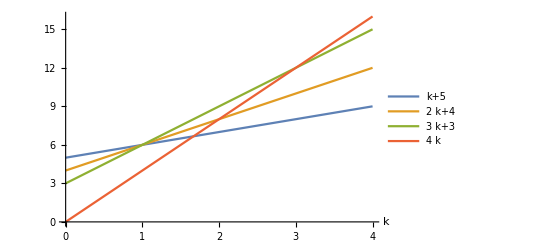

```mathematica
Plot[{k+5,2k+4,3k+3,4k},{k,0,4},PlotLegends->"Expressions",AxesLabel->Automatic]
```

## Single Term Leading Cancellation

In the following, we are going to investigate when does the leading coefficient vanish depending on k.

As shown below, when 
	k < 1, the leading term is k+5, which has coefficient ‘c1k5’
	1 < k < 3, the leading one is 3k+3, where ‘c3k3’ is its coefficient
	k > 3, we have ‘c4k0’ as the coefficient of the leading power
	
Hence, in the following we are going to split into 3 cases.

Under the ansatz, a[r]=r^k, in the following, we show only k > 3 can have single leading term cancellation.
Since the power is too large, it is not physical in two sense: (1) goes to singularity quickly -> (2) cannot connect to exterior Schwarzschild.

### Equation with β

#### k < 1: c1k5 dominates

```mathematica
c1k5//FullSimplify
```

```mathematica
TeXForm[-3 k η^3 (k (-2+η)+η)]
```

-3 \eta ^3 k (\eta +(\eta -2) k)

```mathematica
Solve[c1k5==0,k]
```

{{k→0},{k→-η/(-2+η)}}

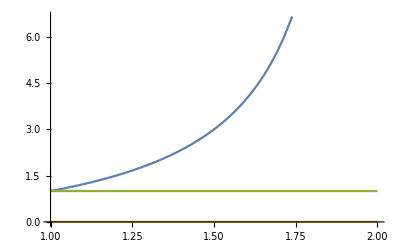

```mathematica
Plot[{η/(2-η),0,1},{η,1,2}]
```

k is always greater than 1 with η in [1, 2], its physical domain.

#### 1 < k < 3: c3k3 dominates

```mathematica
-(η (1+η))/(2-3 η+η^2)//FullSimplify
```

-(η (1+η))/(2-3 η+η^2)

```mathematica
TeXForm[7+4 √3]
```

7+4 \sqrt{3}

```mathematica
Solve[c3k3==0,k]//FullSimplify
```

{{k→0},{k→-(η (1+η))/(2-3 η+η^2)}}

```mathematica
Solve[D[-(η (1+η))/(2-3 η+η^2),η]==0,η]
```

{{η→1/2 (1-√3)},{η→1/2 (1+√3)}}

```mathematica
-(η (1+η))/(2-3 η+η^2)/.{η->1/2 (1+√3)}//FullSimplify
```

7+4 √3

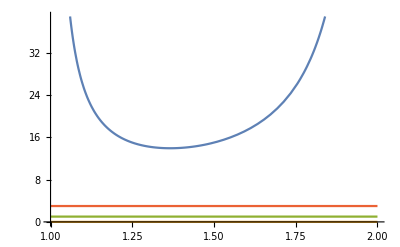

```mathematica
Plot[{-(η (1+η))/(2-3 η+η^2),0,1,3},{η,1,2}]
```

k is always outside [1, 3] for all physical domain of η.

#### k > 3: c4k0 dominates (Interesting + Complicated)

```mathematica
c4k0//FullSimplify
```

36 (α-γ) η^4-k^4 (-2+η) (-1+η) (γ (-2+η) (-1+η)+3 β (1-2 η) η)+3 k η^3 (4 α (7-5 η)+9 β (1+η)+4 γ (-7+5 η))+k^2 η^2 (β (63-99 η)+12 α (-2+η) (-1+2 η)+γ (-73+(106-37 η) η))+k^3 η (2 γ (-2+η) (-1+η) (-7+5 η)+3 β (6+η (-28+(31-7 η) η)))

```mathematica
TeXForm[3 k η^3 (4 α (7-5 η)+9 β (1+η)+4 γ (-7+5 η))]
```

3 \eta ^3 k (4 \alpha  (7-5 \eta )+9 \beta  (\eta +1)+4 \gamma  (5 \eta -7))

```mathematica
TeXForm[36 (α-γ) η^4]
```

36 \eta ^4 (\alpha -\gamma )

```mathematica
ks=Solve[c4k0==0,k];
```

```mathematica
ks=ks/.{α->1,γ->s,β->b};
```

#### (k > 3) Define 4 different k’s into k1, k2, k3, k4

```mathematica
k1[s_,η_,b_]:=-(-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)/(4 (2-3 η+η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2))-1/2 √(-(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/((2-3 η+η^2) (-2 s-3 b η+3 s η+6 b η^2-s η^2))+((-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)^2)/(4 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2)^2)+(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/(3 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4))+(2^(1/3) η^4 (-2+3 η-η^2) (576-1512 b+2511 b^2+1824 s-2394 b s+s^2-2880 η+9504 b η-7128 b^2 η-1632 s η+3240 b s η+4 s^2 η+4752 η^2-14580 b η^2+9072 b^2 η^2-1368 s η^2+2376 b s η^2+6 s^2 η^2-2880 η^3+8208 b η^3-5832 b^2 η^3+1680 s η^3-2880 b s η^3+4 s^2 η^3+576 η^4-1188 b η^4+1701 b^2 η^4-408 s η^4+378 b s η^4+s^2 η^4))/(3 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2) (2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3))+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3)/(3 2^(1/3) (-2+3 η-η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2)))-1/2 √(-(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/((2-3 η+η^2) (-2 s-3 b η+3 s η+6 b η^2-s η^2))+((-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)^2)/(2 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2)^2)-(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/(3 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4))-(2^(1/3) η^4 (-2+3 η-η^2) (576-1512 b+2511 b^2+1824 s-2394 b s+s^2-2880 η+9504 b η-7128 b^2 η-1632 s η+3240 b s η+4 s^2 η+4752 η^2-14580 b η^2+9072 b^2 η^2-1368 s η^2+2376 b s η^2+6 s^2 η^2-2880 η^3+8208 b η^3-5832 b^2 η^3+1680 s η^3-2880 b s η^3+4 s^2 η^3+576 η^4-1188 b η^4+1701 b^2 η^4-408 s η^4+378 b s η^4+s^2 η^4))/(3 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2) (2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3))-(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3)/(3 2^(1/3) (-2+3 η-η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2))-((4 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4))/((2-3 η+η^2)^2 (-2 s-3 b η+3 s η+6 b η^2-s η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2))-((-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)^3)/((2-3 η+η^2)^3 (2 s+3 b η-3 s η-6 b η^2+s η^2)^3)+(24 (28 η^3+9 b η^3-28 s η^3-20 η^4+9 b η^4+20 s η^4))/((2-3 η+η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2)))/(4 √(-(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/((2-3 η+η^2) (-2 s-3 b η+3 s η+6 b η^2-s η^2))+((-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)^2)/(4 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2)^2)+(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/(3 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4))+(2^(1/3) η^4 (-2+3 η-η^2) (576-1512 b+2511 b^2+1824 s-2394 b s+s^2-2880 η+9504 b η-7128 b^2 η-1632 s η+3240 b s η+4 s^2 η+4752 η^2-14580 b η^2+9072 b^2 η^2-1368 s η^2+2376 b s η^2+6 s^2 η^2-2880 η^3+8208 b η^3-5832 b^2 η^3+1680 s η^3-2880 b s η^3+4 s^2 η^3+576 η^4-1188 b η^4+1701 b^2 η^4-408 s η^4+378 b s η^4+s^2 η^4))/(3 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2) (2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3))+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3)/(3 2^(1/3) (-2+3 η-η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2)))))
```

```mathematica
k2[s_,η_,b_]:=-(-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)/(4 (2-3 η+η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2))-1/2 √(-(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/((2-3 η+η^2) (-2 s-3 b η+3 s η+6 b η^2-s η^2))+((-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)^2)/(4 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2)^2)+(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/(3 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4))+(2^(1/3) η^4 (-2+3 η-η^2) (576-1512 b+2511 b^2+1824 s-2394 b s+s^2-2880 η+9504 b η-7128 b^2 η-1632 s η+3240 b s η+4 s^2 η+4752 η^2-14580 b η^2+9072 b^2 η^2-1368 s η^2+2376 b s η^2+6 s^2 η^2-2880 η^3+8208 b η^3-5832 b^2 η^3+1680 s η^3-2880 b s η^3+4 s^2 η^3+576 η^4-1188 b η^4+1701 b^2 η^4-408 s η^4+378 b s η^4+s^2 η^4))/(3 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2) (2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3))+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3)/(3 2^(1/3) (-2+3 η-η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2)))+1/2 √(-(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/((2-3 η+η^2) (-2 s-3 b η+3 s η+6 b η^2-s η^2))+((-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)^2)/(2 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2)^2)-(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/(3 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4))-(2^(1/3) η^4 (-2+3 η-η^2) (576-1512 b+2511 b^2+1824 s-2394 b s+s^2-2880 η+9504 b η-7128 b^2 η-1632 s η+3240 b s η+4 s^2 η+4752 η^2-14580 b η^2+9072 b^2 η^2-1368 s η^2+2376 b s η^2+6 s^2 η^2-2880 η^3+8208 b η^3-5832 b^2 η^3+1680 s η^3-2880 b s η^3+4 s^2 η^3+576 η^4-1188 b η^4+1701 b^2 η^4-408 s η^4+378 b s η^4+s^2 η^4))/(3 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2) (2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3))-(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3)/(3 2^(1/3) (-2+3 η-η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2))-((4 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4))/((2-3 η+η^2)^2 (-2 s-3 b η+3 s η+6 b η^2-s η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2))-((-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)^3)/((2-3 η+η^2)^3 (2 s+3 b η-3 s η-6 b η^2+s η^2)^3)+(24 (28 η^3+9 b η^3-28 s η^3-20 η^4+9 b η^4+20 s η^4))/((2-3 η+η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2)))/(4 √(-(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/((2-3 η+η^2) (-2 s-3 b η+3 s η+6 b η^2-s η^2))+((-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)^2)/(4 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2)^2)+(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/(3 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4))+(2^(1/3) η^4 (-2+3 η-η^2) (576-1512 b+2511 b^2+1824 s-2394 b s+s^2-2880 η+9504 b η-7128 b^2 η-1632 s η+3240 b s η+4 s^2 η+4752 η^2-14580 b η^2+9072 b^2 η^2-1368 s η^2+2376 b s η^2+6 s^2 η^2-2880 η^3+8208 b η^3-5832 b^2 η^3+1680 s η^3-2880 b s η^3+4 s^2 η^3+576 η^4-1188 b η^4+1701 b^2 η^4-408 s η^4+378 b s η^4+s^2 η^4))/(3 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2) (2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3))+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3)/(3 2^(1/3) (-2+3 η-η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2)))))
```

```mathematica
k3[s_,η_,b_]:=-(-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)/(4 (2-3 η+η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2))+1/2 √(-(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/((2-3 η+η^2) (-2 s-3 b η+3 s η+6 b η^2-s η^2))+((-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)^2)/(4 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2)^2)+(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/(3 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4))+(2^(1/3) η^4 (-2+3 η-η^2) (576-1512 b+2511 b^2+1824 s-2394 b s+s^2-2880 η+9504 b η-7128 b^2 η-1632 s η+3240 b s η+4 s^2 η+4752 η^2-14580 b η^2+9072 b^2 η^2-1368 s η^2+2376 b s η^2+6 s^2 η^2-2880 η^3+8208 b η^3-5832 b^2 η^3+1680 s η^3-2880 b s η^3+4 s^2 η^3+576 η^4-1188 b η^4+1701 b^2 η^4-408 s η^4+378 b s η^4+s^2 η^4))/(3 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2) (2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3))+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3)/(3 2^(1/3) (-2+3 η-η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2)))-1/2 √(-(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/((2-3 η+η^2) (-2 s-3 b η+3 s η+6 b η^2-s η^2))+((-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)^2)/(2 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2)^2)-(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/(3 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4))-(2^(1/3) η^4 (-2+3 η-η^2) (576-1512 b+2511 b^2+1824 s-2394 b s+s^2-2880 η+9504 b η-7128 b^2 η-1632 s η+3240 b s η+4 s^2 η+4752 η^2-14580 b η^2+9072 b^2 η^2-1368 s η^2+2376 b s η^2+6 s^2 η^2-2880 η^3+8208 b η^3-5832 b^2 η^3+1680 s η^3-2880 b s η^3+4 s^2 η^3+576 η^4-1188 b η^4+1701 b^2 η^4-408 s η^4+378 b s η^4+s^2 η^4))/(3 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2) (2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3))-(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3)/(3 2^(1/3) (-2+3 η-η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2))+((4 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4))/((2-3 η+η^2)^2 (-2 s-3 b η+3 s η+6 b η^2-s η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2))-((-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)^3)/((2-3 η+η^2)^3 (2 s+3 b η-3 s η-6 b η^2+s η^2)^3)+(24 (28 η^3+9 b η^3-28 s η^3-20 η^4+9 b η^4+20 s η^4))/((2-3 η+η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2)))/(4 √(-(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/((2-3 η+η^2) (-2 s-3 b η+3 s η+6 b η^2-s η^2))+((-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)^2)/(4 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2)^2)+(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/(3 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4))+(2^(1/3) η^4 (-2+3 η-η^2) (576-1512 b+2511 b^2+1824 s-2394 b s+s^2-2880 η+9504 b η-7128 b^2 η-1632 s η+3240 b s η+4 s^2 η+4752 η^2-14580 b η^2+9072 b^2 η^2-1368 s η^2+2376 b s η^2+6 s^2 η^2-2880 η^3+8208 b η^3-5832 b^2 η^3+1680 s η^3-2880 b s η^3+4 s^2 η^3+576 η^4-1188 b η^4+1701 b^2 η^4-408 s η^4+378 b s η^4+s^2 η^4))/(3 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2) (2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3))+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3)/(3 2^(1/3) (-2+3 η-η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2)))))
```

```mathematica
k4[s_,η_,b_]:=-(-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)/(4 (2-3 η+η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2))+1/2 √(-(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/((2-3 η+η^2) (-2 s-3 b η+3 s η+6 b η^2-s η^2))+((-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)^2)/(4 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2)^2)+(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/(3 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4))+(2^(1/3) η^4 (-2+3 η-η^2) (576-1512 b+2511 b^2+1824 s-2394 b s+s^2-2880 η+9504 b η-7128 b^2 η-1632 s η+3240 b s η+4 s^2 η+4752 η^2-14580 b η^2+9072 b^2 η^2-1368 s η^2+2376 b s η^2+6 s^2 η^2-2880 η^3+8208 b η^3-5832 b^2 η^3+1680 s η^3-2880 b s η^3+4 s^2 η^3+576 η^4-1188 b η^4+1701 b^2 η^4-408 s η^4+378 b s η^4+s^2 η^4))/(3 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2) (2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3))+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3)/(3 2^(1/3) (-2+3 η-η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2)))+1/2 √(-(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/((2-3 η+η^2) (-2 s-3 b η+3 s η+6 b η^2-s η^2))+((-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)^2)/(2 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2)^2)-(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/(3 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4))-(2^(1/3) η^4 (-2+3 η-η^2) (576-1512 b+2511 b^2+1824 s-2394 b s+s^2-2880 η+9504 b η-7128 b^2 η-1632 s η+3240 b s η+4 s^2 η+4752 η^2-14580 b η^2+9072 b^2 η^2-1368 s η^2+2376 b s η^2+6 s^2 η^2-2880 η^3+8208 b η^3-5832 b^2 η^3+1680 s η^3-2880 b s η^3+4 s^2 η^3+576 η^4-1188 b η^4+1701 b^2 η^4-408 s η^4+378 b s η^4+s^2 η^4))/(3 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2) (2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3))-(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3)/(3 2^(1/3) (-2+3 η-η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2))+((4 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4))/((2-3 η+η^2)^2 (-2 s-3 b η+3 s η+6 b η^2-s η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2))-((-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)^3)/((2-3 η+η^2)^3 (2 s+3 b η-3 s η-6 b η^2+s η^2)^3)+(24 (28 η^3+9 b η^3-28 s η^3-20 η^4+9 b η^4+20 s η^4))/((2-3 η+η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2)))/(4 √(-(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/((2-3 η+η^2) (-2 s-3 b η+3 s η+6 b η^2-s η^2))+((-18 b η+28 s η+84 b η^2-62 s η^2-93 b η^3+44 s η^3+21 b η^4-10 s η^4)^2)/(4 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2)^2)+(24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)/(3 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4))+(2^(1/3) η^4 (-2+3 η-η^2) (576-1512 b+2511 b^2+1824 s-2394 b s+s^2-2880 η+9504 b η-7128 b^2 η-1632 s η+3240 b s η+4 s^2 η+4752 η^2-14580 b η^2+9072 b^2 η^2-1368 s η^2+2376 b s η^2+6 s^2 η^2-2880 η^3+8208 b η^3-5832 b^2 η^3+1680 s η^3-2880 b s η^3+4 s^2 η^3+576 η^4-1188 b η^4+1701 b^2 η^4-408 s η^4+378 b s η^4+s^2 η^4))/(3 (2-3 η+η^2)^2 (2 s+3 b η-3 s η-6 b η^2+s η^2) (2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3))+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2+√(-4 ((24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^2+432 (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+9 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4))^3+(2 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4)^3+243 (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4)^2 (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)-2592 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (η^4-s η^4) (-4 s-6 b η+12 s η+21 b η^2-13 s η^2-21 b η^3+6 s η^3+6 b η^4-s η^4)+27 (24 η^2+63 b η^2-73 s η^2-60 η^3-99 b η^3+106 s η^3+24 η^4-37 s η^4) (-28 η^3-9 b η^3+28 s η^3+20 η^4-9 b η^4-20 s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)+972 (η^4-s η^4) (18 b η-28 s η-84 b η^2+62 s η^2+93 b η^3-44 s η^3-21 b η^4+10 s η^4)^2)^2))^(1/3)/(3 2^(1/3) (-2+3 η-η^2) (2 s+3 b η-3 s η-6 b η^2+s η^2)))))
```

#### k > 3 - Continue

```mathematica
Manipulate[
Plot[
{
Re[k1[s,η,b]],
Re[k2[s,η,b]],
Re[k3[s,η,b]],
Re[k4[s,η,b]],
3
},
{η,1+0.1,2-0.1},
PlotLegends->{k1,k2,k3,k4,3},PlotRange->All,PlotLegends->Automatic]
,{{b,0},-10,10},{{s,1.1},1/3,31/18}]
```

```mathematica
Manipulate[
Plot[
{
Im[k1[s,η,b]],
Im[k2[s,η,b]],
Im[k3[s,η,b]],
Im[k4[s,η,b]],
0
},
{η,1+0.1,2-0.1},
PlotLegends->{k1,k2,k3,k4,0},PlotRange->All]
,{{b,0},-10,10},{{s,1.1},1/3,31/18}]
```

## Asymptotic Solutions

### Setup for Static Solutions without β

#### Setup

```mathematica
coord={u,r,θ,ϕ};
dim=4;
metricsign=-1;
metric={{-ⅇ^A[r]/B[r],-ⅇ^(A[r]/2),0,0},{-ⅇ^(A[r]/2),0,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
im=Inverse[metric];
```

```mathematica
SetDirectory["C:\\Program Files\\Wolfram Research\\Mathematica\\12.3"]
<<diffgeo.m
```

C:\Program Files\Wolfram Research\Mathematica\12.3

```mathematica
Ein=Einstein;
RS=RicciScalar;
RT=RicciTensor;
Rie=Riemann;
WT=Weyl;
```

```mathematica
GTr=Sum[im[[i,j]] Einstein[[i,j]],{i,1,dim},{j,1,dim}];
GUD=Table[Sum[im[[i,k]] Einstein[[k,j]],{k,1,dim}],{i,1,dim},{j,1,dim}];
RT2=Sum[RT[[i,j]]RT[[a,b]]im[[i,a]]im[[j,b]],{i,1,dim},{j,1,dim},{a,1,dim},{b,1,dim}];
Rie2=Sum[Rie[[i,j,k,l]] Rie[[a,b,c,d]] im[[i,a]]im[[j,b]]im[[k,c]]metric[[l,d]],{i,1,dim},{j,1,dim},{k,1,dim},{l,1,dim},{a,1,dim},{b,1,dim},{c,1,dim},{d,1,dim}];
WT2=Sum[WT[[i,j,k,l]]WT[[a,b,c,d]]im[[i,a]]im[[j,b]]im[[k,c]]im[[l,d]],{i,1,dim},{j,1,dim},{k,1,dim},{l,1,dim},{a,1,dim},{b,1,dim},{c,1,dim},{d,1,dim}];
G=Rie2-4 RT2+RS^2;
```

The semi-classical Einstein equation is:

```mathematica
eq=GTr-(γ WT2-α G);
```

Also for later convenience, the equation of state is given by ‘EoS’ to 0:

```mathematica
eos=(-GUD[[2,2]])/GUD[[1,1]]-(2-η)/η;
```

```mathematica
A[r_]:=2ψ[r] (* ψ[u_,r_]:=-(∫_r)^R0[u]((∂_ρ a[u,ρ])/(ρ-a[u,ρ]))ⅆρ *)
B[r_]:=(1-a[r]/r)^-1
```

```mathematica
psi1=D[a[r], r]/(η(r-a[r]));
psi2=D[psi1,r];
psi3=D[psi2,r];
psi4=D[psi3,r];
```

```mathematica
eqa=eq/.{Derivative[1][ψ][r]->psi1,Derivative[2][ψ][r]->psi2,Derivative[3][ψ][r]->psi3,Derivative[4][ψ][r]->psi4};
```

```mathematica
(* EoM for 2 Branches: *)
(* Br1: '-' in front of square root *)
(* Br2: '+' in front of square root *)
eqaBrs=Solve[2 (-2+η)^2 r^2 γ η (r-a[r])*eqa==0,a''[r]]//FullSimplify
```

{{a''[r]→1/(2 r^4 γ (-2+η)^2 η^2 (r-a[r])^2)(-3 r^7 (-2+η) η^3-√3 √(r^4 (-2+η)^2 η^5 (r-a[r])^4 (3 η (r^6+8 (α-γ) a[r] (-r^3+2 α a[r]))-24 r^4 γ (-1+η) a'[r]+16 r^2 α γ (-2+η) a'[r]^2))+r^2 (-2+η) η (3 η^2 a[r] (2 r^2 (r^2+2 α-2 γ)-r (r^2+8 α-8 γ) a[r]+4 (α-γ) a[r]^2)+2 r γ η (r-a[r]) (4 r (-1+η)+(5-4 η) a[r]) a'[r]+2 r^2 γ (-2+η) (-r+a[r]) a'[r]^2))},{a''[r]→1/(2 r^4 γ (-2+η)^2 η^2 (r-a[r])^2)(-3 r^7 (-2+η) η^3+√3 √(r^4 (-2+η)^2 η^5 (r-a[r])^4 (3 η (r^6+8 (α-γ) a[r] (-r^3+2 α a[r]))-24 r^4 γ (-1+η) a'[r]+16 r^2 α γ (-2+η) a'[r]^2))+r^2 (-2+η) η (3 η^2 a[r] (2 r^2 (r^2+2 α-2 γ)-r (r^2+8 α-8 γ) a[r]+4 (α-γ) a[r]^2)+2 r γ η (r-a[r]) (4 r (-1+η)+(5-4 η) a[r]) a'[r]+2 r^2 γ (-2+η) (-r+a[r]) a'[r]^2))}}

```mathematica
factor=1/(2 r^4 γ (-2+η)^2 η^2 (r-a[r])^2);
normal=-3 r^7 (-2+η) η^3+r^2 (-2+η) η (3 η^2 a[r] (2 r^2 (r^2+2 α-2 γ)-r (r^2+8 α-8 γ) a[r]+4 (α-γ) a[r]^2)+2 r γ η (r-a[r]) (4 r (-1+η)+(5-4 η) a[r]) a'[r]+2 r^2 γ (-2+η) (-r+a[r]) a'[r]^2);
sqrt=√3 √(r^4 (-2+η)^2 η^5 (r-a[r])^4 (3 η (r^6+8 (α-γ) a[r] (-r^3+2 α a[r]))-24 r^4 γ (-1+η) a'[r]+16 r^2 α γ (-2+η) a'[r]^2));
eqbrs=a''[r]-factor*(normal+(-1)^mode*sqrt);
```

```mathematica
sqrt/.{r->Sqrt[(1-(6 α η^4+3 γ (-3+η) (-1+η) (-3+4 η))/(2 α η^2 (-9+(-5+η) (-3+η) η)+γ (-9+η (42+η (-40+η (9+4 η))))))/((η^2 (3+2 (-2+η) η))/(2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2)))]}//FullSimplify
```

```mathematica
a3*r^3+a1*r
a1=(6 α η^4+3 γ (-3+η) (-1+η) (-3+4 η))/(2 α η^2 (-9+(-5+η) (-3+η) η)+γ (-9+η (42+η (-40+η (9+4 η)))))
a3=(η^2 (3+2 (-2+η) η))/(2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2))
```

$Aborted

```mathematica
(1-(6 s η^4+3 (-3+η) (-1+η) (-3+4 η))/(2 s η^2 (-9+(-5+η) (-3+η) η)+ (-9+η (42+η (-40+η (9+4 η))))))/((η^2 (3+2 (-2+η) η))/(2 (-3+η)γ(- (-3+η)+2 s (-1+η) η^2)))//FullSimplify
```

(2 γ (-3+η) (3+η (-1+2 s (-1+η) η)) (1+(27-3 η (24+η (-19+2 η (2+s η))))/(-9+η (42+η (-40+η (9+4 η)+2 s (-9+(-5+η) (-3+η) η))))))/(η^2 (3+2 (-2+η) η))

```mathematica
Manipulate[
Plot3D[{(2 γ (-3+η) (3+η (-1+2 s (-1+η) η)) (1+(27-3 η (24+η (-19+2 η (2+s η))))/(-9+η (42+η (-40+η (9+4 η)+2 s (-9+(-5+η) (-3+η) η))))))/(η^2 (3+2 (-2+η) η)),0},{η,1,2},{s,1/3,31/18},AxesLabel->Automatic],{γ,0,10,0.01}]
```

#### Asymptotic Expansion for Branch 1

```mathematica
a[r_]:=a0+c1/r+c2/r^2+c3/r^3+c4/r^4+c5/r^5+c6/r^6+c7/r^7
Series[eqa,{r,Infinity,10}]//FullSimplify
Clear[a]
```

(2 c1)/(η r^4)-(a0 c1+2 c2 (-4+η))/(η r^5)+(-2 c1^2 (-1+η)-a0^2 c1 η+2 η (-a0 c2-3 c3 (-3+η)+6 a0^2 (α-γ) η))/(η^2 r^6)+1/(η^2 r^7)(c1 c2 (8-7 η)-a0^3 c1 η-2 a0^2 c2 η+4 c4 (8-3 η) η+a0 (c1^2 (2-3 η)-3 c3 η+16 c1 (α-γ) η (-2+3 η)))-1/(3 η^2 r^8)(6 c1^3 (-1+η)+3 a0^4 c1 η+6 a0^3 c2 η+6 c1 c3 (-6+5 η)+3 a0^2 (-2 c1^2+3 c3 η+4 c1 (c1-α+γ) η)+8 c1^2 (2 γ (2-3 η)^2-15 α (-1+η) η)+6 (5 c5 η (-5+2 η)+c2^2 (-4+3 η))+6 a0 (2 (c4-20 c2 (α-γ) (-1+η)) η+c1 c2 (-4+5 η)))+1/(3 η^2 r^9)(72 c2 c3+c1 c4 (48-39 η)+3 c1^2 c2 (10-9 η)-3 a0^5 c1 η-6 a0^4 c2 η-51 c2 c3 η+216 c6 η-90 c6 η^2-8 c1 c2 (9 α (6-5 η) η+20 γ (-1+η) (-2+3 η))-3 a0^3 (3 c3 η+4 c1 (-α+γ) η+c1^2 (-2+5 η))-3 a0^2 (4 (c4+2 c2 (-α+γ)) η+c1 c2 (-8+13 η))+a0 (6 c1 c3 (6-7 η)+3 c1^3 (4-5 η)-24 c2^2 (-1+η)-15 c5 η+72 c3 (α-γ) η (-6+5 η)+4 c1^2 (2 γ (5-6 η)+α (-6+9 η))))-1/(3 η^3 r^10)(6 c1^4 (-1+η) η+c1^3 (16 γ (-1+η) (-2+3 η)+3 η (-8 α (-1+η)+a0^2 (-6+9 η)))+η (6 a0^5 c2 η+9 a0^4 c3 η+12 a0^3 (c4+2 c2 (-α+γ)) η+18 c3^2 (-3+2 η)+42 c7 η (-7+3 η)+6 c2 c4 (-16+11 η)+4 c2^2 (100 γ (-1+η)^2+21 α (4-3 η) η)+3 a0^2 (5 c5 η+12 c3 (-α+γ) η+2 c2^2 (-4+5 η))+6 a0 (3 c6 η+28 c4 (α-γ) (4-3 η) η+c2 c3 (-12+11 η)))+3 c1^2 η (2 c3 (-7+6 η)+a0^4 (-2+6 η)+2 a0 c2 (-10+11 η)+a0^2 (α (8-16 η)+γ (-13+20 η)))+c1 η (3 a0^6 η+12 a0^4 (-α+γ) η+24 a0^3 c2 (-1+2 η)+18 a0^2 c3 (-2+3 η)+6 a0 c4 (-8+9 η)+c2^2 (-48+39 η)+12 (14 c3 α (4-3 η) η+c5 (-5+4 η)+4 c3 γ (-2+3 η) (-6+5 η))+4 a0 c2 (6 α (4-5 η)+γ (-42+43 η))))+O[1/r]^11

```mathematica
c1=c1/.Solve[c1==0,c1]
c2=c2/.Solve[a0 c1+2 c2 (-4+η)==0,c2]//FullSimplify
c3=c3/.Solve[-2 c1^2 (-1+η)-a0^2 c1 η+2 η (-a0 c2-3 c3 (-3+η)+6 a0^2 (α-γ) η)==0,c3]//FullSimplify
c4=c4/.Solve[c1 c2 (8-7 η)-a0^3 c1 η-2 a0^2 c2 η+4 c4 (8-3 η) η+a0 (c1^2 (2-3 η)-3 c3 η+16 c1 (α-γ) η (-2+3 η))==0,c4]//FullSimplify
c5=c5/.Solve[6 c1^3 (-1+η)+3 a0^4 c1 η+6 a0^3 c2 η+6 c1 c3 (-6+5 η)+3 a0^2 (-2 c1^2+3 c3 η+4 c1 (c1-α+γ) η)+8 c1^2 (2 γ (2-3 η)^2-15 α (-1+η) η)+6 (5 c5 η (-5+2 η)+c2^2 (-4+3 η))+6 a0 (2 (c4-20 c2 (α-γ) (-1+η)) η+c1 c2 (-4+5 η))==0,c5]//FullSimplify
c6=c6/.Solve[72 c2 c3+c1 c4 (48-39 η)+3 c1^2 c2 (10-9 η)-3 a0^5 c1 η-6 a0^4 c2 η-51 c2 c3 η+216 c6 η-90 c6 η^2-8 c1 c2 (9 α (6-5 η) η+20 γ (-1+η) (-2+3 η))-3 a0^3 (3 c3 η+4 c1 (-α+γ) η+c1^2 (-2+5 η))-3 a0^2 (4 (c4+2 c2 (-α+γ)) η+c1 c2 (-8+13 η))+a0 (6 c1 c3 (6-7 η)+3 c1^3 (4-5 η)-24 c2^2 (-1+η)-15 c5 η+72 c3 (α-γ) η (-6+5 η)+4 c1^2 (2 γ (5-6 η)+α (-6+9 η)))==0,c6]//FullSimplify
c7=c7/.Solve[6 c1^4 (-1+η) η+c1^3 (16 γ (-1+η) (-2+3 η)+3 η (-8 α (-1+η)+a0^2 (-6+9 η)))+η (6 a0^5 c2 η+9 a0^4 c3 η+12 a0^3 (c4+2 c2 (-α+γ)) η+18 c3^2 (-3+2 η)+42 c7 η (-7+3 η)+6 c2 c4 (-16+11 η)+4 c2^2 (100 γ (-1+η)^2+21 α (4-3 η) η)+3 a0^2 (5 c5 η+12 c3 (-α+γ) η+2 c2^2 (-4+5 η))+6 a0 (3 c6 η+28 c4 (α-γ) (4-3 η) η+c2 c3 (-12+11 η)))+3 c1^2 η (2 c3 (-7+6 η)+a0^4 (-2+6 η)+2 a0 c2 (-10+11 η)+a0^2 (α (8-16 η)+γ (-13+20 η)))+c1 η (3 a0^6 η+12 a0^4 (-α+γ) η+24 a0^3 c2 (-1+2 η)+18 a0^2 c3 (-2+3 η)+6 a0 c4 (-8+9 η)+c2^2 (-48+39 η)+12 (14 c3 α (4-3 η) η+c5 (-5+4 η)+4 c3 γ (-2+3 η) (-6+5 η))+4 a0 c2 (6 α (4-5 η)+γ (-42+43 η)))==0,c7]//FullSimplify
Clear[c1,c2,c3,c4,c5,c6,c7]
```

{0}

{0}

{(2 a0^2 (α-γ) η)/(-3+η)}

{(3 a0^3 (-α+γ) η)/(2 (-3+η) (-8+3 η))}

{(9 a0^4 (-α+γ) η)/(5 (-5+2 η) (-8+3 η))}

{(a0^3 (α-γ) η (-3 a0^2 (-3+η) (-11+4 η)+16 (α-γ) (-5+2 η) (-8+3 η) (-6+5 η)))/(2 (-3+η) (-5+2 η) (-8+3 η) (-12+5 η))}

{-((3 a0^4 (α-γ) η (3 a0^2 (-3+η)^2 (-11+4 η) (-13+5 η)+4 (α-γ) (-5+2 η) (-1584+η (2592+η (-1271+195 η)))))/(14 (-3+η)^2 (-5+2 η) (-8+3 η) (-7+3 η) (-12+5 η)))}

Therefore we get the 1^st asymptotic solution in branch 1 equation:

	a(r)=a0+(2 a0^2 (γ-α) η)/(3-η)1/r^3+(3 a0^3 (γ-α) η)/(2 (3-η) (8-3 η))1/r^4+(9 a0^4 (γ-α) η)/(5 (5-2 η) (8-3 η))1/r^5+...

where a0 is a free parameter representing the Schwarzschild radius at large r.

Check that it is indeed a Branch 1 solution, not Branch 2:

```mathematica
a[r_]:=a0;

Series[normal,{r,Infinity,-5}]//FullSimplify
Series[sqrt,{r,Infinity,-5}]//FullSimplify

Clear[a]
```

3 η^2 r^5+1/O[1/r]^4

3 η √(η^2) r^5+1/O[1/r]^4

The ‘-‘ branch converges to 0 at large r, and therefore, this asymptotic solution belongs to branch 1.

#### Asymptotic Expansion for Branch 1’

```mathematica
a[r_]:=a1*r+a0+c1/r+c2/r^2+c3/r^3+c4/r^4+c5/r^5+c6/r^6

Series[eqa,{r,Infinity,9}]//FullSimplify

Clear[a]
```

(2 a1 (-1+(-a1/(-1+a1)+η)/η^2))/r^2+(a0 a1 (-a1 (-2+η)+η))/((-1+a1)^2 η^2 r^3)+1/(3 (-1+a1)^3 η^4 r^4)(-4 (-1+a1) a1^4 γ-16 (-1+a1)^2 a1^3 γ η+2 a1 (-3 a0^2 a1+(-1+a1) ((-6+9 a1) c1+4 (-1+a1) a1 (3 a1 α+2 γ-3 a1 γ))) η^2+(-1+a1) (6 c1+a1 (3 a0^2-6 c1+8 (-1+a1)^2 a1 (3 α-2 γ))) η^3-4 (-1+a1)^3 a1^2 γ η^4)-1/(3 ((-1+a1)^4 η^4) r^5)(3 a0^3 a1 (a1 (-2+η)-η) η^2+3 (-1+a1)^2 c2 η^2 (2 (4-5 a1) a1-(-1+a1) (-8+5 a1) η+2 (-1+a1)^2 η^2)+a0 (-1+a1) (-8 a1^4 γ-12 (-1+a1) a1^3 γ η+4 a1 ((-3+6 a1) c1+2 (-1+a1) a1 (3 α-4 γ+3 a1 γ)) η^2+(-1+a1) ((3-12 a1) c1-4 (-1+a1) a1 (3 (-4+5 a1) α+12 γ-13 a1 γ)) η^3+24 (-1+a1)^3 a1 (-α+γ) η^4))+1/(3 (-1+a1)^5 η^4 r^6)(3 a0^4 a1 (a1 (-2+η)-η) η^2+6 a0 (-1+a1)^2 c2 η^2 (a1 (4+3 a1 (-2+η)-4 η)+η)+2 (-1+a1)^2 (4 a1^3 (-2+3 a1) c1 γ+4 (-1+a1) a1^2 (-8+9 a1) c1 γ η+(-3 (1-2 a1)^2 c1^2+3 (-1+a1) a1 (-6+7 a1) c3-4 (-1+a1) a1 c1 (a1 (-3+6 a1) α-8 γ+(10-3 a1) a1 γ)) η^2+(-1+a1) ((-3+6 a1) c1^2+3 (-1+a1) (-9+7 a1) c3+4 (-1+a1) a1 c1 (3 a1 α+8 γ-9 a1 γ)) η^3+3 (-1+a1)^3 (-3 c3+4 a1 c1 (3 α-2 γ)) η^4)+a0^2 (-1+a1) (-12 a1^4 γ-8 (-1+a1) a1^3 γ η+a1 (6 (-2+5 a1) c1+(-1+a1) a1 (24 α-31 γ+23 a1 γ)) η^2-(-1+a1) (3 (-1+5 a1) c1+4 (-1+a1) a1 (3 α-3 γ+2 a1 γ)) η^3+36 (-1+a1)^4 (α-γ) η^4))-1/(3 ((-1+a1)^6 η^4) r^7)(-3 a0^5 a1 η^2 (-a1 (-2+η)+η)+3 a0^2 (-1+a1)^2 c2 η^2 (a1 (8+7 a1 (-2+η)-9 η)+2 η)-a0^3 (-1+a1) (16 a1^4 γ+4 (-1+a1) a1^3 γ η-2 a1 (6 (-1+3 a1) c1+(-1+a1) a1 (12 α+(-15+11 a1) γ)) η^2+(-1+a1) (3 (-1+6 a1) c1+4 (-1+a1) a1 (3 α+(-3+2 a1) γ)) η^3)+a0 (-1+a1)^2 (8 a1^3 (-4+7 a1) c1 γ+4 (-1+a1) a1^2 (-13+15 a1) c1 γ η-2 (3 (1-6 a1+8 a1^2) c1^2-6 (-1+a1) a1 (-3+4 a1) c3+2 (-1+a1) a1 c1 (12 (-1+2 a1) α+(18+11 a1 (-5+3 a1)) γ)) η^2+(-1+a1) (3 (-3+8 a1) (c1^2+c3-a1 c3)+12 (-1+a1) (8+a1 (-14+9 a1)) c1 α-4 (-1+a1) (24+a1 (-37+16 a1)) c1 γ) η^3+144 (-1+a1)^4 c1 (-α+γ) η^4)+(-1+a1)^3 (8 (4-5 a1) a1^3 c2 γ-4 (-1+a1) a1^2 (-36+37 a1) c2 γ η+2 (6 (2+a1 (-7+6 a1)) c1 c2+(-1+a1) a1 (3 (8-9 a1) c4+12 a1 (-3+4 a1) c2 α-4 (-4+3 a1) (-5+4 a1) c2 γ)) η^2+(-1+a1) (3 (7-12 a1) c1 c2+(-1+a1) ((96-81 a1) c4+4 a1 c2 (3 (-8+5 a1) α+(-20+23 a1) γ))) η^3+4 (-1+a1)^3 (9 c4+4 a1 c2 (-9 α+5 γ)) η^4))+1/(3 (-1+a1)^7 η^4 r^8)(3 a0^6 a1 (a1 (-2+η)-η) η^2+6 a0^3 (-1+a1)^2 c2 η^2 (a1 (4+4 a1 (-2+η)-5 η)+η)+a0^4 (-1+a1) (-20 a1^4 γ+a1 (6 (-2+7 a1) c1+(-1+a1) a1 (24 α+(-29+21 a1) γ)) η^2-(-1+a1) (3 (-1+7 a1) c1+4 (-1+a1) a1 (3 α+(-3+2 a1) γ)) η^3)+a0^2 (-1+a1)^2 (48 a1^3 (-1+2 a1) c1 γ+40 (-1+a1)^2 a1^2 c1 γ η-2 (3 (1+a1 (-8+13 a1)) c1^2-9 (-1+a1) a1 (-2+3 a1) c3+(-1+a1) a1 c1 (12 (-2+5 a1) α+(35+a1 (-121+74 a1)) γ)) η^2+(-1+a1) (3 (-4+13 a1) c1^2-9 (-1+a1) (-1+3 a1) c3+4 (-1+a1) c1 (3 (-1+5 a1) α+(3+a1 (-20+13 a1)) γ)) η^3)+2 a0 (-1+a1)^3 (4 (8-11 a1) a1^3 c2 γ-60 (-1+a1)^2 a1^2 c2 γ η+(6 (2+a1 (-10+11 a1)) c1 c2+(-1+a1) a1 (6 (4-5 a1) c4+24 (-2+3 a1) c2 α+(76+3 a1 (-67+39 a1)) c2 γ)) η^2+(-1+a1) (3 (5-11 a1) c1 c2+(-1+a1) (3 (-2+5 a1) c4+2 c2 (-6 (10+a1 (-19+11 a1)) α+(60+a1 (-103+47 a1)) γ))) η^3+120 (-1+a1)^4 c2 (α-γ) η^4)-(-1+a1)^3 (4 a1^2 ((6+a1 (-20+17 a1)) c1^2-2 (-1+a1) a1 (-6+7 a1) c3) γ-40 (-1+a1)^2 a1 ((2-3 a1) c1^2+6 (-1+a1) a1 c3) γ η-2 (3 (1-2 a1)^2 c1^3-6 (-1+a1) (-1+2 a1) (-3+4 a1) c1 c3+2 (-1+a1) c1^2 (6 a1 (-1+a1+a1^2) α+(16+a1 (-14+a1 (-31+27 a1))) γ)+(-1+a1) (-3 (2-3 a1)^2 c2^2-(-1+a1) a1 ((30-33 a1) c5+4 c3 (3 a1 (-5+6 a1) α-36 γ+(59-24 a1) a1 γ)))) η^2+(-1+a1) (6 (-1+2 a1) c1^3-6 (-1+a1) (-5+8 a1) c1 c3+8 (-1+a1) c1^2 (3 (5+2 a1 (-5+3 a1)) α+(-24+(43-20 a1) a1) γ)+(-1+a1) (9 (2-3 a1) c2^2+2 (-1+a1) ((75-66 a1) c5+8 a1 c3 (3 (-5+4 a1) α+(-6+7 a1) γ)))) η^3+12 (-1+a1)^4 (5 c5+10 a1 c3 (-2 α+γ)+2 c1^2 (-5 α+6 γ)) η^4))-1/(3 ((-1+a1)^8 η^4) r^9)(3 a0^7 a1 (a1 (-2+η)-η) η^2+3 a0^4 (-1+a1)^2 c2 η^2 (a1 (8+9 a1 (-2+η)-11 η)+2 η)+a0^5 (-1+a1) (-24 a1^4 γ+4 (-1+a1) a1^3 γ η+4 a1 (3 (-1+4 a1) c1+(-1+a1) a1 (6 α+(-7+5 a1) γ)) η^2-(-1+a1) (3 (-1+8 a1) c1+4 (-1+a1) a1 (3 α+(-3+2 a1) γ)) η^3)+a0^3 (-1+a1)^2 (16 a1^3 (-4+9 a1) c1 γ+4 (-1+a1) a1^2 (-7+3 a1) c1 γ η-2 ((3-30 a1+57 a1^2) c1^2-6 (-1+a1) a1 (-3+5 a1) c3+(-1+a1) a1 c1 (24 (-1+3 a1) α+(34+a1 (-131+81 a1)) γ)) η^2+(-1+a1) (3 (-5+19 a1) c1^2-3 (-1+a1) (-3+10 a1) c3+4 (-1+a1) c1 (3 (-1+6 a1) α+(3+a1 (-23+15 a1)) γ)) η^3)-a0^2 (-1+a1)^3 (48 a1^3 (-2+3 a1) c2 γ+12 (-1+a1) a1^2 (-8+7 a1) c2 γ η-2 (6 (2+a1 (-13+17 a1)) c1 c2+(-1+a1) a1 ((24-33 a1) c4+12 (-4+7 a1) c2 α+(74+a1 (-209+123 a1)) c2 γ)) η^2+(-1+a1) (3 (-13+34 a1) c1 c2+(-1+a1) ((12-33 a1) c4+4 c2 (3 (-2+7 a1) α+(6+a1 (-32+21 a1)) γ))) η^3)+a0 (-1+a1)^3 (24 a1^2 (-2 (1-2 a1)^2 c1^2+(-1+a1) a1 (-4+5 a1) c3) γ+4 (-1+a1) a1 ((-17+4 (12-7 a1) a1) c1^2+(-1+a1) a1 (-51+49 a1) c3) γ η+2 (6 (1+a1 (-5+6 a1)) c1^3-6 (-1+a1) (3+14 (-1+a1) a1) c1 c3+4 (-1+a1) c1^2 (3 (1-6 a1+8 a1^2) α+(-5+a1 (40+a1 (-79+41 a1))) γ)+(-1+a1) (-3 (-2+3 a1) (-2+5 a1) c2^2-2 (-1+a1) a1 (3 (5-6 a1) c5+12 (-3+4 a1) c3 α+4 (15-38 a1+22 a1^2) c3 γ))) η^2+(-1+a1) ((15-36 a1) c1^3+42 (-1+a1) (-1+2 a1) c1 c3-4 (-1+a1) c1^2 (3 (-3+8 a1) α+(12+a1 (-45+28 a1)) γ)+(-1+a1) (3 (-8+15 a1) c2^2+(-1+a1) ((15-36 a1) c5+12 (36+a1 (-70+39 a1)) c3 α-4 (108+a1 (-192+89 a1)) c3 γ))) η^3+360 (-1+a1)^5 c3 (-α+γ) η^4)+(-1+a1)^4 (-8 a1^2 (-3 (2-3 a1)^2 c1 c2+(-1+a1) a1 (-8+9 a1) c4) γ-4 (-1+a1) a1 ((-88+9 (23-13 a1) a1) c1 c2+(-1+a1) a1 (-88+87 a1) c4) γ η-2 (3 (-1+2 a1) (-5+8 a1) c1^2 c2+2 (-1+a1) c1 (-3 (-1+2 a1) (-4+5 a1) c4+12 a1 (-1+2 a1^2) c2 α+(80+3 a1 (-38+a1 (-13+23 a1))) c2 γ)+(-1+a1) (-6 (-2+3 a1) (-3+4 a1) c2 c3+(-1+a1) a1 ((-36+39 a1) c6+12 (7-8 a1) a1 c4 α+4 (56+a1 (-94+39 a1)) c4 γ))) η^2+(-1+a1) (3 (-9+16 a1) c1^2 c2+(-1+a1) c1 ((39-60 a1) c4+12 (36+a1 (-74+43 a1)) c2 α-4 (200+3 a1 (-123+58 a1)) c2 γ)+(-1+a1) (3 (17-24 a1) c2 c3+(-1+a1) (3 (72-65 a1) c6+4 a1 c4 (-108 α+93 a1 α-28 γ+33 a1 γ)))) η^3+6 (-1+a1)^4 (15 c6-60 (c1 c2+a1 c4) α+4 (20 c1 c2+7 a1 c4) γ) η^4))+O[1/r]^10

```mathematica
a1=a1/.Solve[-1+(-a1/(-1+a1)+η)/η^2==0,a1]//FullSimplify
a0=a0/.Solve[a0 a1 (-a1 (-2+η)+η)==0,a0]//FullSimplify
c1=c1/.Solve[-4 (-1+a1) a1^4 γ-16 (-1+a1)^2 a1^3 γ η+2 a1 (-3 a0^2 a1+(-1+a1) ((-6+9 a1) c1+4 (-1+a1) a1 (3 a1 α+2 γ-3 a1 γ))) η^2+(-1+a1) (6 c1+a1 (3 a0^2-6 c1+8 (-1+a1)^2 a1 (3 α-2 γ))) η^3-4 (-1+a1)^3 a1^2 γ η^4==0,c1]//FullSimplify
c2=c2/.Solve[3 a0^3 a1 (a1 (-2+η)-η) η^2+3 (-1+a1)^2 c2 η^2 (2 (4-5 a1) a1-(-1+a1) (-8+5 a1) η+2 (-1+a1)^2 η^2)+a0 (-1+a1) (-8 a1^4 γ-12 (-1+a1) a1^3 γ η+4 a1 ((-3+6 a1) c1+2 (-1+a1) a1 (3 α-4 γ+3 a1 γ)) η^2+(-1+a1) ((3-12 a1) c1-4 (-1+a1) a1 (3 (-4+5 a1) α+12 γ-13 a1 γ)) η^3+24 (-1+a1)^3 a1 (-α+γ) η^4)==0,c2]//FullSimplify

c3=c3/.Solve[3 a0^4 a1 (a1 (-2+η)-η) η^2+6 a0 (-1+a1)^2 c2 η^2 (a1 (4+3 a1 (-2+η)-4 η)+η)+2 (-1+a1)^2 (4 a1^3 (-2+3 a1) c1 γ+4 (-1+a1) a1^2 (-8+9 a1) c1 γ η+(-3 (1-2 a1)^2 c1^2+3 (-1+a1) a1 (-6+7 a1) c3-4 (-1+a1) a1 c1 (a1 (-3+6 a1) α-8 γ+(10-3 a1) a1 γ)) η^2+(-1+a1) ((-3+6 a1) c1^2+3 (-1+a1) (-9+7 a1) c3+4 (-1+a1) a1 c1 (3 a1 α+8 γ-9 a1 γ)) η^3+3 (-1+a1)^3 (-3 c3+4 a1 c1 (3 α-2 γ)) η^4)+a0^2 (-1+a1) (-12 a1^4 γ-8 (-1+a1) a1^3 γ η+a1 (6 (-2+5 a1) c1+(-1+a1) a1 (24 α-31 γ+23 a1 γ)) η^2-(-1+a1) (3 (-1+5 a1) c1+4 (-1+a1) a1 (3 α-3 γ+2 a1 γ)) η^3+36 (-1+a1)^4 (α-γ) η^4)==0,c3]//FullSimplify
c4=c4/.Solve[-3 a0^5 a1 η^2 (-a1 (-2+η)+η)+3 a0^2 (-1+a1)^2 c2 η^2 (a1 (8+7 a1 (-2+η)-9 η)+2 η)-a0^3 (-1+a1) (16 a1^4 γ+4 (-1+a1) a1^3 γ η-2 a1 (6 (-1+3 a1) c1+(-1+a1) a1 (12 α+(-15+11 a1) γ)) η^2+(-1+a1) (3 (-1+6 a1) c1+4 (-1+a1) a1 (3 α+(-3+2 a1) γ)) η^3)+a0 (-1+a1)^2 (8 a1^3 (-4+7 a1) c1 γ+4 (-1+a1) a1^2 (-13+15 a1) c1 γ η-2 (3 (1-6 a1+8 a1^2) c1^2-6 (-1+a1) a1 (-3+4 a1) c3+2 (-1+a1) a1 c1 (12 (-1+2 a1) α+(18+11 a1 (-5+3 a1)) γ)) η^2+(-1+a1) (3 (-3+8 a1) (c1^2+c3-a1 c3)+12 (-1+a1) (8+a1 (-14+9 a1)) c1 α-4 (-1+a1) (24+a1 (-37+16 a1)) c1 γ) η^3+144 (-1+a1)^4 c1 (-α+γ) η^4)+(-1+a1)^3 (8 (4-5 a1) a1^3 c2 γ-4 (-1+a1) a1^2 (-36+37 a1) c2 γ η+2 (6 (2+a1 (-7+6 a1)) c1 c2+(-1+a1) a1 (3 (8-9 a1) c4+12 a1 (-3+4 a1) c2 α-4 (-4+3 a1) (-5+4 a1) c2 γ)) η^2+(-1+a1) (3 (7-12 a1) c1 c2+(-1+a1) ((96-81 a1) c4+4 a1 c2 (3 (-8+5 a1) α+(-20+23 a1) γ))) η^3+4 (-1+a1)^3 (9 c4+4 a1 c2 (-9 α+5 γ)) η^4)==0,c4]//FullSimplify

c5=c5/.Solve[3 a0^6 a1 (a1 (-2+η)-η) η^2+6 a0^3 (-1+a1)^2 c2 η^2 (a1 (4+4 a1 (-2+η)-5 η)+η)+a0^4 (-1+a1) (-20 a1^4 γ+a1 (6 (-2+7 a1) c1+(-1+a1) a1 (24 α+(-29+21 a1) γ)) η^2-(-1+a1) (3 (-1+7 a1) c1+4 (-1+a1) a1 (3 α+(-3+2 a1) γ)) η^3)+a0^2 (-1+a1)^2 (48 a1^3 (-1+2 a1) c1 γ+40 (-1+a1)^2 a1^2 c1 γ η-2 (3 (1+a1 (-8+13 a1)) c1^2-9 (-1+a1) a1 (-2+3 a1) c3+(-1+a1) a1 c1 (12 (-2+5 a1) α+(35+a1 (-121+74 a1)) γ)) η^2+(-1+a1) (3 (-4+13 a1) c1^2-9 (-1+a1) (-1+3 a1) c3+4 (-1+a1) c1 (3 (-1+5 a1) α+(3+a1 (-20+13 a1)) γ)) η^3)+2 a0 (-1+a1)^3 (4 (8-11 a1) a1^3 c2 γ-60 (-1+a1)^2 a1^2 c2 γ η+(6 (2+a1 (-10+11 a1)) c1 c2+(-1+a1) a1 (6 (4-5 a1) c4+24 (-2+3 a1) c2 α+(76+3 a1 (-67+39 a1)) c2 γ)) η^2+(-1+a1) (3 (5-11 a1) c1 c2+(-1+a1) (3 (-2+5 a1) c4+2 c2 (-6 (10+a1 (-19+11 a1)) α+(60+a1 (-103+47 a1)) γ))) η^3+120 (-1+a1)^4 c2 (α-γ) η^4)-(-1+a1)^3 (4 a1^2 ((6+a1 (-20+17 a1)) c1^2-2 (-1+a1) a1 (-6+7 a1) c3) γ-40 (-1+a1)^2 a1 ((2-3 a1) c1^2+6 (-1+a1) a1 c3) γ η-2 (3 (1-2 a1)^2 c1^3-6 (-1+a1) (-1+2 a1) (-3+4 a1) c1 c3+2 (-1+a1) c1^2 (6 a1 (-1+a1+a1^2) α+(16+a1 (-14+a1 (-31+27 a1))) γ)+(-1+a1) (-3 (2-3 a1)^2 c2^2-(-1+a1) a1 ((30-33 a1) c5+4 c3 (3 a1 (-5+6 a1) α-36 γ+(59-24 a1) a1 γ)))) η^2+(-1+a1) (6 (-1+2 a1) c1^3-6 (-1+a1) (-5+8 a1) c1 c3+8 (-1+a1) c1^2 (3 (5+2 a1 (-5+3 a1)) α+(-24+(43-20 a1) a1) γ)+(-1+a1) (9 (2-3 a1) c2^2+2 (-1+a1) ((75-66 a1) c5+8 a1 c3 (3 (-5+4 a1) α+(-6+7 a1) γ)))) η^3+12 (-1+a1)^4 (5 c5+10 a1 c3 (-2 α+γ)+2 c1^2 (-5 α+6 γ)) η^4)==0,c5]//FullSimplify

c6=c6/.Solve[3 a0^7 a1 (a1 (-2+η)-η) η^2+3 a0^4 (-1+a1)^2 c2 η^2 (a1 (8+9 a1 (-2+η)-11 η)+2 η)+a0^5 (-1+a1) (-24 a1^4 γ+4 (-1+a1) a1^3 γ η+4 a1 (3 (-1+4 a1) c1+(-1+a1) a1 (6 α+(-7+5 a1) γ)) η^2-(-1+a1) (3 (-1+8 a1) c1+4 (-1+a1) a1 (3 α+(-3+2 a1) γ)) η^3)+a0^3 (-1+a1)^2 (16 a1^3 (-4+9 a1) c1 γ+4 (-1+a1) a1^2 (-7+3 a1) c1 γ η-2 ((3-30 a1+57 a1^2) c1^2-6 (-1+a1) a1 (-3+5 a1) c3+(-1+a1) a1 c1 (24 (-1+3 a1) α+(34+a1 (-131+81 a1)) γ)) η^2+(-1+a1) (3 (-5+19 a1) c1^2-3 (-1+a1) (-3+10 a1) c3+4 (-1+a1) c1 (3 (-1+6 a1) α+(3+a1 (-23+15 a1)) γ)) η^3)-a0^2 (-1+a1)^3 (48 a1^3 (-2+3 a1) c2 γ+12 (-1+a1) a1^2 (-8+7 a1) c2 γ η-2 (6 (2+a1 (-13+17 a1)) c1 c2+(-1+a1) a1 ((24-33 a1) c4+12 (-4+7 a1) c2 α+(74+a1 (-209+123 a1)) c2 γ)) η^2+(-1+a1) (3 (-13+34 a1) c1 c2+(-1+a1) ((12-33 a1) c4+4 c2 (3 (-2+7 a1) α+(6+a1 (-32+21 a1)) γ))) η^3)+a0 (-1+a1)^3 (24 a1^2 (-2 (1-2 a1)^2 c1^2+(-1+a1) a1 (-4+5 a1) c3) γ+4 (-1+a1) a1 ((-17+4 (12-7 a1) a1) c1^2+(-1+a1) a1 (-51+49 a1) c3) γ η+2 (6 (1+a1 (-5+6 a1)) c1^3-6 (-1+a1) (3+14 (-1+a1) a1) c1 c3+4 (-1+a1) c1^2 (3 (1-6 a1+8 a1^2) α+(-5+a1 (40+a1 (-79+41 a1))) γ)+(-1+a1) (-3 (-2+3 a1) (-2+5 a1) c2^2-2 (-1+a1) a1 (3 (5-6 a1) c5+12 (-3+4 a1) c3 α+4 (15-38 a1+22 a1^2) c3 γ))) η^2+(-1+a1) ((15-36 a1) c1^3+42 (-1+a1) (-1+2 a1) c1 c3-4 (-1+a1) c1^2 (3 (-3+8 a1) α+(12+a1 (-45+28 a1)) γ)+(-1+a1) (3 (-8+15 a1) c2^2+(-1+a1) ((15-36 a1) c5+12 (36+a1 (-70+39 a1)) c3 α-4 (108+a1 (-192+89 a1)) c3 γ))) η^3+360 (-1+a1)^5 c3 (-α+γ) η^4)+(-1+a1)^4 (-8 a1^2 (-3 (2-3 a1)^2 c1 c2+(-1+a1) a1 (-8+9 a1) c4) γ-4 (-1+a1) a1 ((-88+9 (23-13 a1) a1) c1 c2+(-1+a1) a1 (-88+87 a1) c4) γ η-2 (3 (-1+2 a1) (-5+8 a1) c1^2 c2+2 (-1+a1) c1 (-3 (-1+2 a1) (-4+5 a1) c4+12 a1 (-1+2 a1^2) c2 α+(80+3 a1 (-38+a1 (-13+23 a1))) c2 γ)+(-1+a1) (-6 (-2+3 a1) (-3+4 a1) c2 c3+(-1+a1) a1 ((-36+39 a1) c6+12 (7-8 a1) a1 c4 α+4 (56+a1 (-94+39 a1)) c4 γ))) η^2+(-1+a1) (3 (-9+16 a1) c1^2 c2+(-1+a1) c1 ((39-60 a1) c4+12 (36+a1 (-74+43 a1)) c2 α-4 (200+3 a1 (-123+58 a1)) c2 γ)+(-1+a1) (3 (17-24 a1) c2 c3+(-1+a1) (3 (72-65 a1) c6+4 a1 c4 (-108 α+93 a1 α-28 γ+33 a1 γ)))) η^3+6 (-1+a1)^4 (15 c6-60 (c1 c2+a1 c4) α+4 (20 c1 c2+7 a1 c4) γ) η^4)==0,c6]//FullSimplify

Clear[a0,a1,c1,c2,c3,c4,c5,c6]
```

{((-1+η) η)/(1+(-1+η) η)}

{0}

{(2 (-1+η)^2 η (3 γ+2 α (-2+η) η))/((1+(-1+η) η)^2 (3+(-2+η) η (1+η)))}

{0}

{-((4 (-1+η)^3 η (3 γ+2 α (-2+η) η) (-2 α η (1+η (-13+η (10+η (5+2 (-4+η) η))))+γ (33+η (-72+η (23+η (-5+2 η) (-7+η (2+η)))))))/((1+(-1+η) η)^3 (15-10 η+η^3) (3+(-2+η) η (1+η))^2))}

{0}

{(8 (-1+η)^4 η (3 γ+2 α (-2+η) η) (36 α^2 (-1+η) η^2 (169+η (-186+η (-63+η (85+η (111+η (-94+η (-45+η (69+η (-25+3 η)))))))))+3 γ^2 (-1+η) (-6048+η (17226+η (-11673+η (-8517+η (13649+η (-2365+η (-3783+η (1717+η (187+η (-180+η (2+5 η)))))))))))+2 α γ η (-4995+η (29268+η (-50994+η (22560+η (28004+η (-33898+η (5416+η (9029+η (-4931+η (320+η (304+η (-49+(-5+η) η))))))))))))))/(3 (1+(-1+η) η)^4 (15-10 η+η^3) (3+(-2+η) η (1+η))^3 (35+η (-22+η+η^2)))}

{0}

Therefore we get the 2^nd asymptotic solution in branch 1 equation:

	a(r)=
((-1+η) η)/(1+(-1+η) η)r+(2 (η-1)^2 η (3 γ-2 α (2-η) η))/((1+(η-1) η)^2 (3-(2-η) η (1+η)))1/r+O(1/r^3)
	
Note that the coefficient of the leading term can never be 1, which separates this linear solution with the branch 2 one (slope-1), as we will see later.

Check that it is indeed a Branch 1 solution, not Branch 2:

```mathematica
a[r_]:=((-1+η) η)/(1+(-1+η) η)r+(2 (η-1)^2 η (3 γ-2 α (2-η) η))/((1+(η-1) η)^2 (3-(2-η) η (1+η)))1/r;

Series[normal,{r,Infinity,-5}]//FullSimplify
Series[sqrt,{r,Infinity,-5}]//FullSimplify

Clear[a,η]
```

(3 η^2 r^5)/(1+(-1+η) η)^2+1/O[1/r]^4

(3 η √(η^2) r^5)/(1+(-1+η) η)^2+1/O[1/r]^4

The ‘-‘ branch converges to 0 at large r, and therefore, this asymptotic solution belongs to branch 1.

#### Asymptotic Expansion for Branch 1’’

```mathematica
a[r_]:=a3*r^3+a1*r+c1/r+c2/r^2+c3/r^3+c4/r^4+c5/r^5+c6/r^6

Series[eqa,{r,Infinity,9}]//FullSimplify

Clear[a]
```

-(6 (a3 (η^2 (3+2 (-2+η) η)+2 a3 (-3+η) (γ (-3+η)-2 α (-1+η) η^2))))/η^4+1/(η^4 r^2)(-2 η^2 (9-3 η+a1 (-3+η+η^2))+8 a3 (-3+η) (α (-3+a1 (-2+η)) η^2+γ (9-3 η+a1 (-3+η (4+η)))))+1/(3 a3 η^4 r^4)(6 (-3+2 a1) (3+a1 (-2+η)-η) η^2+72 a3^2 c1 (2 α (-1+η) η^2+γ (-3+η) (-5+η+2 η^2))+6 a3 η^2 (c1 (15-6 η)+4 α (9-3 η+a1 (-3+a1+(2+a1) η)))-4 a3 γ (27 (-3+η)^2-6 a1 (-3+η) (-15+η (9+η))+a1^2 (81+(-2+η) η (42+η (10+η)))))+(c2 (η^2 (42-η (11+2 η))+4 a3 (α η^2 (-24+η (17+2 η))+γ (-3+η) (-42+η (-1+20 η)))))/(η^4 r^5)+1/(3 a3^2 η^4 r^6)(-6 (-1+a1) (-3+2 a1) (3+a1 (-2+η)-η) η^2+72 a3^3 c3 (α η^2 (-6+η (3+η))+γ (-3+η) (-9+η (-2+5 η)))+4 a3 (3 η^2 (c1 (12+4 a1 (-2+η)-5 η)-2 (-3+2 a1) α (3-2 a1+(-1+a1) η))+2 (-3+2 a1) γ (3+a1 (-2+η)-η) (-6 (-3+η)+a1 (-12+η (7+η))))+6 a3^2 (-3 c3 η^2 (-9+η+η^2)+4 c1 (γ (-3+η) (-39+η (13+6 η))+α η^2 (-15+7 η+a1 (-2+η+3 η^2))-a1 γ (63+η (-63+η+9 η^2+2 η^3)))))+1/(3 a3 η^4 r^7)(15 c2 (12+4 a1 (-2+η)-5 η) η^2+36 a3^2 c4 (α η^2 (-16+η (5+4 η))+γ (-3+η) (-22+η (-9+14 η)))+a3 (9 c4 η^2 (22+η-4 η^2)+4 c2 (3 α η^2 (-42+19 η+a1 (-8+η (-5+12 η)))+γ (6 (-3+η) (-51+2 η (6+5 η))+a1 (-486+η (465+η (46-η (79+20 η))))))))+1/(3 a3^3 η^4 r^8)(6 (-1+a1)^2 (-3+2 a1) (3+a1 (-2+η)-η) η^2+24 a3^4 c5 (2 α η^2 (-15+η (2+5 η))+γ (-3+η) (-39+η (-23+28 η)))+2 a3^2 (9 c3 (12+4 a1 (-2+η)-5 η) η^2+24 c1^2 (-2+η) η^2+8 c1 (3 α η^2 (-12+8 a1+5 η-4 a1 η)+γ (36 (3-2 a1)^2-5 (-3+2 a1) (-15+14 a1) η+2 (-1+a1) (-6+7 a1) η^2+(9+10 (-2+a1) a1) η^3)))-2 a3 (3 η^2 (c1 (-33+a1 (52+10 a1 (-2+η)-23 η)+13 η)-4 (-1+a1) (-3+2 a1) α (3-2 a1+(-1+a1) η))+2 (-3+2 a1) γ (3+a1 (-2+η)-η) (15 (-3+η)+a1 (72-η (31+2 η)+2 a1 (-14+η (8+η)))))-6 a3^3 (c5 η^2 (-39+2 η (-4+5 η))+c1^2 (-4 α (-1+η) η^2 (-1+5 η)+γ (342+2 η (-110+η (-41+12 η (1+η)))))+4 c3 (α η^2 (27-12 η+a1 (6+2 (4-5 η) η))+γ (-3 (-3+η) (-21+η (3+5 η))+a1 (99+η (-90+η (-20+η (18+5 η))))))))+1/(3 a3^2 η^4 r^9)(3 c2 η^2 (78-31 η+a1 (-124-24 a1 (-2+η)+55 η))+36 a3^3 c6 (α η^2 (3+2 η) (-8+5 η)+γ (-3+η) (-30+η (-23+24 η)))+3 a3^2 (3 c6 η^2 (30+(11-10 η) η)+4 c4 (α η^2 (-66+29 η+a1 (-16+η (-31+30 η)))+γ (2 (-3+η) (-75+η (4+21 η))-a1 (-3+2 η) (-78+η (15+η (34+7 η)))))+4 c1 c2 (α η^2 (8+η (-43+30 η))+γ (-450+η (237+η (145-2 η (9+20 η))))))+a3 (21 c4 (12+4 a1 (-2+η)-5 η) η^2+20 c2 (3 η^2 (2 c1 (-2+η)+α (-12+8 a1+5 η-4 a1 η))+γ (6 a1^2 (-2+η) (4+η) (-3+2 η)+3 (-3+η) (-36+η (11+4 η))-a1 (432+η (-336+η (4+25 η)))))))+O[1/r]^10

```mathematica
a3sol=a3/.Flatten[Solve[η^2 (3+2 (-2+η) η)+2 a3 (-3+η) (γ (-3+η)-2 α (-1+η) η^2)==0,a3]]//FullSimplify
a1sol=a1/.Flatten[Solve[-2 η^2 (9-3 η+a1 (-3+η+η^2))+8 a3 (-3+η) (α (-3+a1 (-2+η)) η^2+γ (9-3 η+a1 (-3+η (4+η))))==0,a1]]/.a3->a3sol//FullSimplify
c1sol=c1/.Flatten[Solve[6 (-3+2 a1) (3+a1 (-2+η)-η) η^2+72 a3^2 c1 (2 α (-1+η) η^2+γ (-3+η) (-5+η+2 η^2))+6 a3 η^2 (c1 (15-6 η)+4 α (9-3 η+a1 (-3+a1+(2+a1) η)))-4 a3 γ (27 (-3+η)^2-6 a1 (-3+η) (-15+η (9+η))+a1^2 (81+(-2+η) η (42+η (10+η))))==0,c1]]/.{a3->a3sol,a1->a1sol}//FullSimplify
c2sol=c2/.Flatten[Solve[c2 (η^2 (42-η (11+2 η))+4 a3 (α η^2 (-24+η (17+2 η))+γ (-3+η) (-42+η (-1+20 η))))==0,c2]]/.{a3->a3sol,a1->a1sol,c1->c1sol}//FullSimplify
c3sol=c3/.Flatten[Solve[-6 (-1+a1) (-3+2 a1) (3+a1 (-2+η)-η) η^2+72 a3^3 c3 (α η^2 (-6+η (3+η))+γ (-3+η) (-9+η (-2+5 η)))+4 a3 (3 η^2 (c1 (12+4 a1 (-2+η)-5 η)-2 (-3+2 a1) α (3-2 a1+(-1+a1) η))+2 (-3+2 a1) γ (3+a1 (-2+η)-η) (-6 (-3+η)+a1 (-12+η (7+η))))+6 a3^2 (-3 c3 η^2 (-9+η+η^2)+4 c1 (γ (-3+η) (-39+η (13+6 η))+α η^2 (-15+7 η+a1 (-2+η+3 η^2))-a1 γ (63+η (-63+η+9 η^2+2 η^3))))==0,c3]]/.{a3->a3sol,a1->a1sol,c1->c1sol,c2->c2sol}//FullSimplify

Clear[a3,a1,c1,c2,c3,c4,c5,c6]
```

(η^2 (3+2 (-2+η) η))/(2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2))

(6 α η^4+3 γ (-3+η) (-1+η) (-3+4 η))/(2 α η^2 (-9+(-5+η) (-3+η) η)+γ (-9+η (42+η (-40+η (9+4 η)))))

(2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2) (8 α^3 η^9 (81+η (-297+η (414+η (-294+η (104+(-18+η) η)))))+6 α γ^2 (-3+η) η^2 (486+η (-2349+η (5292+η (-6795+η (5298+η (-2827+η (1569+η (-1087+η (545+8 η (-17+2 η))))))))))+12 α^2 γ η^4 (729+η (-4131+η (11259+η (-18900+η (20961+η (-15594+η (7700+η (-2453+η (494+η (-59+4 η))))))))))+γ^3 (-3+η)^2 (243+η (-972+η (1755+η (-1683+η (1152+η (-908+η (672+η (-283+4 η (35+4 η (-9+4 η))))))))))))/((3+2 (-2+η) η) (2 α (-1+η) η^2 (3+η) (-3+2 η)+γ (-3+η) (-15+η (35+2 η (-7-6 η+4 η^2)))) (2 α η^3 (-9+(-5+η) (-3+η) η)+γ η (-9+η (42+η (-40+η (9+4 η)))))^2)

0

(4 (-3+η)^2 (γ (-3+η)-2 α (-1+η) η^2)^2 (-32 α^5 η^14 (6561+η (-41553+η (123201+η (-220401+η (257823+η (-201258+η (101736+η (-29673+η (2804+η (875+η (-257+16 η)))))))))))+16 α^4 γ η^8 (-531441+η (4251528+η (-15825132+η (35941158+η (-54817155+η (57863646+η (-41332113+η (17581536+η (-1711125+η (-2492262+η (1005903+η (408831+η (-520394+η (221859+η (-53051+4 η (1974+η (-185+6 η)))))))))))))))))+8 α^3 γ^2 η^6 (3720087+η (-31000725+η (130557339+η (-370847403+η (793060875+η (-1339909290+η (1824453720+η (-2014391268+η (1801816569+2 η (-649365093+η (373882230+η (-170028561+η (60362318+η (-16591055+η (3523625+8 η (-71737+η (8527+8 η (-80+3 η))))))))))))))))))+2 α γ^4 (-3+η)^2 η^2 (59049+η (413343+η (-3083670+η (7958493+η (-8446923+η (-6228333+η (36696159+η (-65934270+η (76065327+η (-67459368+η (52410893+η (-38299881+η (25624301+16 η (-917684+η (427655+4 η (-38357+2 η (4809+8 η (-89+6 η))))))))))))))))))+γ^5 (-3+η)^3 (-39366+η (380538+η (-1406241+η (2816856+η (-3051351+η (936927+η (2193885+η (-4016673+η (4254909+η (-3976141+η (3400600+η (-2408311+4 η (372077+η (-241931+2 η (79567+32 η (-1327+η (523+4 η (-37+6 η))))))))))))))))))+4 α^2 γ^3 (-3+η) η^4 (1594323+η (-11042163+η (40232052+η (-101682378+η (197258652+η (-310379040+η (413352477+η (-481247325+2 η (248510673+η (-226417356+η (178440627+η (-118343438+η (63871474+η (-26947651+4 η (2118277+η (-469561+2 η (34499+16 η (-193+9 η))))))))))))))))))))/(3 η^4 (1+η) (3+2 (-2+η) η)^2 (γ (-3+η) (-3+4 η) (9+η (-13+5 η))+2 α η^2 (9+η (-15+η (4+η)))) (2 α (-1+η) η^2 (3+η) (-3+2 η)+γ (-3+η) (-15+η (35+2 η (-7-6 η+4 η^2)))) (2 α η^2 (-9+(-5+η) (-3+η) η)+γ (-9+η (42+η (-40+η (9+4 η)))))^3)

```mathematica
a[r_]:=a3*r^3+a1*r+c1/r+c3/r^3;

Series[(2*D[a[r], r])/(η(r-a[r])),{r,Infinity,3}]//FullSimplify

Clear[a]
```

-6/(η r)+(-6+4 a1)/(a3 η r^3)+O[1/r]^4

```mathematica
ⅇ^A[r]~ⅇ^(-6/η Log[r])=r^(-6/η);
```

```mathematica
(**************************************)
```

```mathematica
a[r_]:=a3sol*r^3+a1sol*r+c1sol/r;

Series[eqa,{r,Infinity,7}]//FullSimplify

Clear[a]
```

(8 (-3+η) (γ (-3+η)-2 α (-1+η) η^2) (-32 α^5 η^14 (6561+η (-41553+η (123201+η (-220401+η (257823+η (-201258+η (101736+η (-29673+η (2804+η (875+η (-257+16 η)))))))))))+16 α^4 γ η^8 (-531441+η (4251528+η (-15825132+η (35941158+η (-54817155+η (57863646+η (-41332113+η (17581536+η (-1711125+η (-2492262+η (1005903+η (408831+η (-520394+η (221859+η (-53051+4 η (1974+η (-185+6 η)))))))))))))))))+8 α^3 γ^2 η^6 (3720087+η (-31000725+η (130557339+η (-370847403+η (793060875+η (-1339909290+η (1824453720+η (-2014391268+η (1801816569+2 η (-649365093+η (373882230+η (-170028561+η (60362318+η (-16591055+η (3523625+8 η (-71737+η (8527+8 η (-80+3 η))))))))))))))))))+2 α γ^4 (-3+η)^2 η^2 (59049+η (413343+η (-3083670+η (7958493+η (-8446923+η (-6228333+η (36696159+η (-65934270+η (76065327+η (-67459368+η (52410893+η (-38299881+η (25624301+16 η (-917684+η (427655+4 η (-38357+2 η (4809+8 η (-89+6 η))))))))))))))))))+γ^5 (-3+η)^3 (-39366+η (380538+η (-1406241+η (2816856+η (-3051351+η (936927+η (2193885+η (-4016673+η (4254909+η (-3976141+η (3400600+η (-2408311+4 η (372077+η (-241931+2 η (79567+32 η (-1327+η (523+4 η (-37+6 η))))))))))))))))))+4 α^2 γ^3 (-3+η) η^4 (1594323+η (-11042163+η (40232052+η (-101682378+η (197258652+η (-310379040+η (413352477+η (-481247325+2 η (248510673+η (-226417356+η (178440627+η (-118343438+η (63871474+η (-26947651+4 η (2118277+η (-469561+2 η (34499+16 η (-193+9 η))))))))))))))))))))/(η^6 (3+2 (-2+η) η)^2 (2 α (-1+η) η^2 (3+η) (-3+2 η)+γ (-3+η) (-15+η (35+2 η (-7-6 η+4 η^2)))) (2 α η^2 (-9+(-5+η) (-3+η) η)+γ (-9+η (42+η (-40+η (9+4 η)))))^3 r^6)+O[1/r]^8

Therefore we get an asymptotic solution:

	a(r)=
(η^2 (3+2 (-2+η) η))/(2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2))r^3+(6 α η^4+3 γ (-3+η) (-1+η) (-3+4 η))/(2 α η^2 (-9+(-5+η) (-3+η) η)+γ (-9+η (42+η (-40+η (9+4 η)))))r+O(1/r)
	
Note that the coefficient of r^3 and r terms are (in physical regime):

```mathematica
(* Coefficient of O(r^3) *)
Plot3D[{(η^2 (3+2 (-2+η) η))/(2 (-3+η) (-(-3+η)+2 s (-1+η) η^2)),0},{s,1,31/18},{η,1,1.5}]
```

-Graphics3D-

```mathematica
(* Coefficient of O(r) *)
Plot3D[{(6 s η^4+3 (-3+η) (-1+η) (-3+4 η))/(2 s η^2 (-9+(-5+η) (-3+η) η)+ (-9+η (42+η (-40+η (9+4 η))))),0},{s,1/3,31/18},{η,1,2}]
```

-Graphics3D-

```mathematica
a[r_]:=a3sol*r^3+a1sol*r;

Series[eqbrs,{r,Infinity,0},Assumptions->1<=η<=2&&α>0&&γ>0&&1/3<α/γ<31/18]//FullSimplify

Clear[a,η,a3sol,a1sol,c1sol,c3sol]
```

(3 η (2 α η^4+γ (-3+η) (-1+η) (-3+4 η)+(-1)^mode √((2 α η^4+γ (-3+η) (-1+η) (-3+4 η))^2)) r)/(2 γ (-3+η) (-2+η) (γ (-3+η)-2 α (-1+η) η^2))+O[1/r]^1

where the term in the bracket of the square root without power 2 is always positive:

```mathematica
Plot3D[{2 s η^4+(-3+η) (-1+η) (-3+4 η),0},{s,1/3,31/18},{η,1,2}]
```

-Graphics3D-

Therefore we get the relevant part to determine which branch it belongs to to be:  	
	2 α η^4+γ (-3+η) (-1+η) (-3+4 η)+(-1)^mode (2 α η^4+γ (-3+η) (-1+η) (-3+4 η))=0
That concludes the solution to be in branch 1!

#### Asymptotic Expansion for Branch 2

```mathematica
a[r_]:=r+c1/r+c2/r^2+c3/r^3+c4/r^4+c5/r^5

Series[eqa,{r,Infinity,6}]//FullSimplify

Clear[a]
```

$Aborted

```mathematica
c1=c1/.Solve[4 γ+6 c1 η^2==0,c1]//FullSimplify
c2=c2/.Solve[2 c2 (4 γ+3 c1 η^2)==0,c2]//FullSimplify
c3=c3/.Solve[4 (4 c1^3-3 c2^2+2 c1 c3) γ-24 c1^3 γ η+2 c1 (-3 c2^2+c1 (3 c3+2 c1 (3 c1+6 α-2 γ))) η^2-6 c1^4 η^4==0,c3]//FullSimplify
c4=c4/.Solve[-12 c1 c2 c3 (2 γ+c1 η^2)+2 c1^2 c4 (4 γ+3 c1 η^2)+2 c2^3 (8 γ+3 c1 η^2)+c1^3 c2 η (-3 (8 α+c1 (-4+η)) η+4 γ (5+2 η))==0,c4]//FullSimplify
c5=c5/.Solve[20 c2^4 γ+6 c1^7 (1-2 η) η^2+6 c1^5 c3 (-4+η) η^2+6 c1 (-8 c2^2 c3 γ+c2^4 η^2)+6 c1^2 (2 c3^2 γ+4 c2 c4 γ-3 c2^2 c3 η^2)+2 c1^3 (-4 c5 γ+3 c3^2 η^2+6 c2 c4 η^2+4 c2^2 (-3 α η^2+γ (2+η (2+η))))-c1^4 (3 (2 c5+c2^2 (-4+η)) η^2+8 c3 (-3 α η^2+γ (2+η (2+η))))+4 c1^6 (6 α (1-2 η) η^2+γ (6+η (-22+η (17+η (6+η)))))==0,c5]//FullSimplify

Clear[a0,a1,c1,c2,c3,c4,c5,c6]
```

{-(2 γ)/(3 η^2)}

{0}

{(4 γ (-6 α η^2+γ (-2+η (6+η))))/(9 η^4)}

{0}

{(8 γ (-36 α^2 η^4+6 α γ η^2 (-7+η (15+η))-γ^2 (13+η (-58+η (55+η (13+η))))))/(27 η^6)}

Therefore we get an asymptotic solution in branch 2 equation:

		a(r)=r-(2 γ)/(3 η^2)1/r+(4 γ (-6 α η^2+γ (-2+η (6+η))))/(9 η^4)1/r^3+(8 γ (-36 α^2 η^4+6 α γ η^2 (-7+η (15+η))-γ^2 (13+η (-58+η (55+η (13+η))))))/(27 η^6)1/r^5+...
	
Check that it is indeed a Branch 2 solution, not Branch 1:

```mathematica
a[r_]:=r-(2 γ)/(3 η^2)1/r+(4 γ (-6 α η^2+γ (-2+η (6+η))))/(9 η^4)1/r^3;

Series[normal,{r,Infinity,0}]//FullSimplify
Series[sqrt,{r,Infinity,0}]//FullSimplify

Clear[a,temp,temp1,temp2]
```

-(4 γ^2 r)/(3 η^2)+O[1/r]^1

(4 γ^2 √(η^2) r)/(3 η^3)+O[1/r]^1

The ‘+‘ branch converges to 0 at large r, and therefore, this asymptotic solution belongs to branch 2.

## Sec 3.2 -- Properties

## Setup

```mathematica
coord={t,r,θ,ϕ};
dim=4;
metricsign=-1;
metric={{-ⅇ^A[r]/B[r],0,0,0},{0,B[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
im=Inverse[metric];
```

```mathematica
SetDirectory["C:\\Program Files\\Wolfram Research\\Mathematica\\13.0"]
<<diffgeo.m
```

C:\Program Files\Wolfram Research\Mathematica\13.0

ds2 = B[r] dd[r]^2-(ⅇ^A[r] dd[t]^2)/B[r]+r^2 (dd[θ]^2+dd[ϕ]^2 Sin[θ]^2)

```mathematica
Ein=Einstein;
RS=RicciScalar;
RT=RicciTensor;
Rie=Riemann;
WT=Weyl;
Christ=Christoffel;
```

```mathematica
GTr=Sum[im[[i,j]] Einstein[[i,j]],{i,1,dim},{j,1,dim}];
GUD=Table[Sum[im[[i,k]] Einstein[[k,j]],{k,1,dim}],{i,1,dim},{j,1,dim}];
RT2=Sum[RT[[i,j]]RT[[a,b]]im[[i,a]]im[[j,b]],{i,1,dim},{j,1,dim},{a,1,dim},{b,1,dim}];
Rie2=Sum[Rie[[i,j,k,l]] Rie[[a,b,c,d]] im[[i,a]]im[[j,b]]im[[k,c]]metric[[l,d]],{i,1,dim},{j,1,dim},{k,1,dim},{l,1,dim},{a,1,dim},{b,1,dim},{c,1,dim},{d,1,dim}];
WT2=Sum[WT[[i,j,k,l]]WT[[a,b,c,d]]im[[i,a]]im[[j,b]]im[[k,c]]im[[l,d]],{i,1,dim},{j,1,dim},{k,1,dim},{l,1,dim},{a,1,dim},{b,1,dim},{c,1,dim},{d,1,dim}];
G=Rie2-4 RT2+RS^2;
BoxR=scalarLaplacian[RS];
```

The semi-classical Einstein equation is:

```mathematica
eq=GTr-(γ WT2-α G+β BoxR);
```

Also for later convenience, the equation of state is given by ‘EoS’ to 0:

```mathematica
eos=(-GUD[[2,2]])/GUD[[1,1]]-(2-η)/η;
```

```mathematica
A[r_]:=2ψ[r] (* ψ[u_,r_]:=-(∫_r)^R0[u]((∂_ρ a[u,ρ])/(ρ-a[u,ρ]))ⅆρ *)
B[r_]:=(1-a[r]/r)^-1
```

```mathematica
psi1=D[a[r], r]/(η(r-a[r]));
psi2=D[psi1,r];
psi3=D[psi2,r];
psi4=D[psi3,r];
```

## Branch 1

### Metric

```mathematica
a[r_]:=a0+(2 a0^2 (α-γ) η)/(-3+η)1/r^3(*+(6 a0^3 (α-γ))/(-3+η)1/r^4+(3 a0^2 (α-γ) (-60 β (-3+η) η+a0^2 (-68+25 η)))/(5 (-3+η) (-5+2 η))1/r^5*);
```

```mathematica
DSolve[{M'[r]==(2 D[a[r], r])/(η(r-a[r]))},M[r],r]//FullSimplify
```

{{M[r]→(η C[1]+6 Log[r]-6 RootSum[2 a0^2 α η-2 a0^2 γ η-3 a0 #1^3+a0 η #1^3+3 #1^4-η #1^4&,(a0 Log[r-#1]-Log[r-#1] #1)/(3 a0-4 #1)&])/η}}

```mathematica
(* Coefficient of dt^2 *)
Series[-(1-a[r]/r)ⅇ^((η C[1]+6 Log[r]-6 RootSum[2 a0^2 α η-2 a0^2 γ η-3 a0 #1^3+a0 η #1^3+3 #1^4-η #1^4&,(a0 Log[r-#1]-Log[r-#1] #1)/(3 a0-4 #1)&])/η),{r,Infinity,4}]//Normal//FullSimplify
```

ⅇ^C[1] (-1+(a0 (r^3+(a0 (α-γ) (-3+2 η))/(-3+η)))/r^4)

```mathematica
(* Coefficient of dr^2 *)
Series[(1-a[r]/r),{r,Infinity,4}]//Normal//FullSimplify
```

1+(a0 (-r^3+(2 a0 (-α+γ) η)/(-3+η)))/r^4

```mathematica
Clear[a]
```

### Einstein and Curvature

```mathematica
a[r_]:=a0+(2 a0^2 (α-γ) η)/(-3+η)1/r^3+(6 a0^3 (α-γ))/(-3+η)1/r^4+(3 a0^2 (α-γ) (-60 β (-3+η) η+a0^2 (-68+25 η)))/(5 (-3+η) (-5+2 η))1/r^5;
```

```mathematica
Series[(GUD/.{Derivative[1][ψ][r]->psi1,Derivative[2][ψ][r]->psi2,Derivative[3][ψ][r]->psi3,Derivative[4][ψ][r]->psi4}),{r,Infinity,6}]//FullSimplify//Normal//MatrixForm
```

((6 a0^2 (α-γ) η)/(r^6 (-3+η)) | 0 | 0 | 0
0 | (6 a0^2 (α-γ) (-2+η))/(r^6 (-3+η)) | 0 | 0
0 | 0 | -(12 a0^2 (α-γ) (-2+η))/(r^6 (-3+η)) | 0
0 | 0 | 0 | -(12 a0^2 (α-γ) (-2+η))/(r^6 (-3+η)))

```mathematica
(* -R *)
Series[GTr,{r,Infinity,6}]/.{Derivative[1][ψ][r]->psi1,Derivative[2][ψ][r]->psi2,Derivative[3][ψ][r]->psi3,Derivative[4][ψ][r]->psi4}//FullSimplify//Normal
```

(12 a0^2 (-α+γ))/r^6

```mathematica
(* Subscript[R, abcd]^2 *)
Series[Rie2,{r,Infinity,10}]/.{Derivative[1][ψ][r]->psi1,Derivative[2][ψ][r]->psi2,Derivative[3][ψ][r]->psi3,Derivative[4][ψ][r]->psi4}//FullSimplify//Normal
```

(12 a0^2)/r^6+(48 a0^3 (α-γ) (-6+5 η))/(r^9 (-3+η))+(24 a0^4 (α-γ) (-56+43 η))/(r^10 (-3+η) η)

```mathematica
(* Subscript[R, ab]^2 *)
Series[RT2,{r,Infinity,12}]/.{Derivative[1][ψ][r]->psi1,Derivative[2][ψ][r]->psi2,Derivative[3][ψ][r]->psi3,Derivative[4][ψ][r]->psi4}//FullSimplify//Normal
```

(72 a0^4 (α-γ)^2 (18+η (-18+5 η)))/(r^12 (-3+η)^2)

```mathematica
Clear[a]
```

## Branch 1’

### Metric

```mathematica
a[r_]:=(-η+η^2)/(1-η+η^2) r+(2 (-1+η)^2 η (3 γ+2 α (-2+η) η))/((1+(-1+η) η)^2 (3+(-2+η) η (1+η)))1/r
```

```mathematica
DSolve[{M'[r]==(2 D[a[r], r])/(η(r-a[r]))},M[r],r]//FullSimplify
```

{{M[r]→C[1]+(2 Log[r])/η+(-1-1/η+η) Log[-2 (-1+η)^2 η (3 γ+2 α (-2+η) η)+r^2 (3+η (-5+4 η-2 η^3+η^4))]}}

```mathematica
(* Coefficient of dt^2 *)
Series[-(1-a[r]/r)ⅇ^(C[1]+(2 Log[r])/η+(-1-1/η+η) Log[-2 (-1+η)^2 η (3 γ+2 α (-2+η) η)+r^2 (3+η (-5+4 η-2 η^3+η^4))]),{r,Infinity,0}]//Normal//FullSimplify
```

-(ⅇ^C[1] r^(-2+2 η) (3+η (-5+4 η-2 η^3+η^4))^(-1-1/η+η))/(1+(-1+η) η)

```mathematica
(* Coefficient of dr^2 *)
Series[(1-a[r]/r)^-1,{r,Infinity,0}]//Normal//FullSimplify
```

1+(-1+η) η

```mathematica
Clear[a]
```

### Einstein and Curvature

```mathematica
a[r_]:=(-η+η^2)/(1-η+η^2) r+(2 (-1+η)^2 η (3 γ+2 α (-2+η) η))/((1+(-1+η) η)^2 (3+(-2+η) η (1+η)))1/r+((4 (-1+η)^2 η (3 γ+2 α (-2+η) η) (2 β (-4+η) (3+(-2+η) η (1+η))^2-(-1+η) (-2 α η (1+η (-13+η (10+η (5+2 (-4+η) η))))+γ (33+η (-72+η (23+η (-5+2 η) (-7+η (2+η))))))))/((1+(-1+η) η)^3 (15-10 η+η^3) (3+(-2+η) η (1+η))^2))1/r^3+((8 (-1+η)^2 η (3 γ+2 α (-2+η) η) (18 β^2 (-6+η) (-4+η) (15-10 η+η^3) (3+(-2+η) η (1+η))^3+6 β (-1+η) (3+(-2+η) η (1+η))^2 (α η (-594+η (2329+η (-1836+η (101+η (396+(-8+η) η (17+η))))))+γ (2169+η (-4812+η (2638+η (436+η (-737+η (124-5 (-5+η) η)))))))+(-1+η)^2 (36 α^2 (-1+η) η^2 (169+η (-186+η (-63+η (85+η (111+η (-94+η (-45+η (69+η (-25+3 η)))))))))+3 γ^2 (-1+η) (-6048+η (17226+η (-11673+η (-8517+η (13649+η (-2365+η (-3783+η (1717+η (187+η (-180+η (2+5 η)))))))))))+2 α γ η (-4995+η (29268+η (-50994+η (22560+η (28004+η (-33898+η (5416+η (9029+η (-4931+η (320+η (304+η (-49+(-5+η) η)))))))))))))))/(3 (1+(-1+η) η)^4 (15-10 η+η^3) (3+(-2+η) η (1+η))^3 (35+η (-22+η+η^2))))1/r^5;
```

```mathematica
Series[(GUD/.{Derivative[1][ψ][r]->psi1,Derivative[2][ψ][r]->psi2,Derivative[3][ψ][r]->psi3,Derivative[4][ψ][r]->psi4}),{r,Infinity,2}]//FullSimplify//Normal//MatrixForm
```

((-1+1/(1+(-1+η) η))/r^2 | 0 | 0 | 0
0 | -((-2+η) (-1+η))/(r^2 (1+(-1+η) η)) | 0 | 0
0 | 0 | (1-η/(1+(-1+η) η))/r^2 | 0
0 | 0 | 0 | (1-η/(1+(-1+η) η))/r^2)

```mathematica
(* R *)
Series[GTr,{r,Infinity,4}]/.{Derivative[1][ψ][r]->psi1,Derivative[2][ψ][r]->psi2,Derivative[3][ψ][r]->psi3,Derivative[4][ψ][r]->psi4}//FullSimplify//Normal
```

(4 (-1+η)^2 (3 γ+2 α (-2+η) η))/(r^4 (1+(-1+η) η)^2)

```mathematica
(* Subscript[R, abcd]^2 *)
Series[Rie2,{r,Infinity,6}]/.{Derivative[1][ψ][r]->psi1,Derivative[2][ψ][r]->psi2,Derivative[3][ψ][r]->psi3,Derivative[4][ψ][r]->psi4}//FullSimplify//Normal
```

(8 (-1+η)^2 (3+(-2+η) η))/(r^4 (1+(-1+η) η)^2)+(16 (-1+η)^3 (3 γ+2 α (-2+η) η) (-12+η (17+η (-2+(-3+η) η))))/(r^6 (1+(-1+η) η)^3 (3+(-2+η) η (1+η)))

```mathematica
(* Subscript[R, ab]^2 *)
Series[RT2,{r,Infinity,6}]/.{Derivative[1][ψ][r]->psi1,Derivative[2][ψ][r]->psi2,Derivative[3][ψ][r]->psi3,Derivative[4][ψ][r]->psi4}//FullSimplify//Normal
```

(2 (-1+η)^2 (3+2 (-2+η) η))/(r^4 (1+(-1+η) η)^2)+(8 (-2+η) (-1+η)^3 (3 γ+2 α (-2+η) η) (3-3 η+η^3))/(r^6 (1+(-1+η) η)^3 (3+(-2+η) η (1+η)))

```mathematica
Clear[a]
```

## Branch 1’’

### Metric

```mathematica
(* k=(η^2 (3+2 (-2+η) η))/(2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2)) *)
a[r_]:=k*r^3
```

```mathematica
DSolve[{M'[r]==(2 D[a[r], r])/(η(r-a[r]))},M[r],r]//FullSimplify
```

{{M[r]→C[1]-(3 Log[-1+k r^2])/η}}

```mathematica
(* Coefficient of dt^2 *)
Series[-(1-a[r]/r)ⅇ^(C[1]-(3 Log[-1+k r^2])/η),{r,Infinity,0}]//Normal//FullSimplify
```

(ⅇ^C[1] k^(-3/η) r^(-6/η) (3+(-1+k r^2) η))/η

```mathematica
(* Coefficient of dr^2 *)
(1-a[r]/r)^-1//FullSimplify
```

1/(1-k r^2)

```mathematica
Clear[a]
```

### Einstein and Curvature

```mathematica
(* k=(η^2 (3+2 (-2+η) η))/(2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2)) *)
a[r_]:=k*r^3+l*r+m/r;
```

```mathematica
Series[(GUD/.{Derivative[1][ψ][r]->psi1,Derivative[2][ψ][r]->psi2,Derivative[3][ψ][r]->psi3,Derivative[4][ψ][r]->psi4}),{r,Infinity,2}]//FullSimplify//Normal//MatrixForm
```

(-3 k-l/r^2 | 0 | 0 | 0
0 | (l (-1+2/η))/r^2-(3 k (-2+η))/η | 0 | 0
0 | 0 | (-9+3 l+3 η-2 l η)/(r^2 η^2)-(3 k (3+(-3+η) η))/η^2 | 0
0 | 0 | 0 | (-9+3 l+3 η-2 l η)/(r^2 η^2)-(3 k (3+(-3+η) η))/η^2)

```mathematica
(* R *)
Series[(GTr/.{Derivative[1][ψ][r]->psi1,Derivative[2][ψ][r]->psi2,Derivative[3][ψ][r]->psi3,Derivative[4][ψ][r]->psi4}),{r,Infinity,4}]//FullSimplify//Normal
```

-(6 k (3+2 (-2+η) η))/η^2+(l (24-10 η)+4 l^2 (-2+η)+6 (-3+k m (5-2 η)+η))/(k r^4 η^2)-(2 (9-3 η+l (-3+η+η^2)))/(r^2 η^2)

```mathematica
(* Subscript[R, abcd]^2 *)
Series[(Rie2/.{Derivative[1][ψ][r]->psi1,Derivative[2][ψ][r]->psi2,Derivative[3][ψ][r]->psi3,Derivative[4][ψ][r]->psi4}),{r,Infinity,4}]//FullSimplify//Normal
```

(12 k^2 (27+2 η (-18+η (12+(-4+η) η))))/η^4+(4 (-3 (-3+η)^2 (-9+2 η)+2 l (-3+η) (45+η (-36+5 η))-6 k m (45+2 η (-21+η (3+η)))+l^2 (81+η (-102+η (43+(-4+η) η)))))/(r^4 η^4)+(8 k (-3 (-3+η)^3+l (-27+η (45+η (-15+η+η^2)))))/(r^2 η^4)

```mathematica
(* Subscript[R, ab]^2 *)
Series[(RT2/.{Derivative[1][ψ][r]->psi1,Derivative[2][ψ][r]->psi2,Derivative[3][ψ][r]->psi3,Derivative[4][ψ][r]->psi4}),{r,Infinity,4}]//FullSimplify//Normal
```

(18 k^2 (3+(-2+η) η) (3+2 (-2+η) η))/η^4+(12 k (-3 (-3+η) (3+(-3+η) η)+l (-9+η (15-7 η+η^3))))/(r^2 η^4)+(12 l (-45+η (60+η (-29+5 η)))+2 l^2 (81+η (-120+η (66+(-14+η) η)))+6 (-3 (-3+η) (9+η (-7+2 η))+2 k m (-45+η (60+η (-29+4 η)))))/(r^4 η^4)

```mathematica
Clear[a]
```

## Branch 2

### Metric

```mathematica
a[r_]:=r-(2 γ)/(3 η^2)1/r
```

```mathematica
(* Calculate A[r] in ⅇ^A[r] where M[r]=A[r] *)
DSolve[{M'[r]==(2 D[a[r], r])/(η(r-a[r]))},M[r],r]//FullSimplify
```

{{M[r]→(3 r^2 η)/(2 γ)+C[1]+(2 Log[r])/η}}

```mathematica
(* Coefficient of dt^2 *)
-(1-a[r]/r)ⅇ^((3 r^2 η)/(2 γ)+C[1]+(2 Log[r])/η)//FullSimplify
```

-(2 ⅇ^((3 r^2 η)/(2 γ)+C[1]) r^(-2+2/η) γ)/(3 η^2)

```mathematica
(* Coefficient of dr^2 *)
(1-a[r]/r)^-1//FullSimplify
```

(3 r^2 η^2)/(2 γ)

```mathematica
Clear[a]
```

### Einstein and Curvature

```mathematica
a[r_]:=r-(2 γ)/(3 η^2)1/r;
```

```mathematica
Series[(GUD/.{Derivative[1][ψ][r]->psi1,Derivative[2][ψ][r]->psi2,Derivative[3][ψ][r]->psi3,Derivative[4][ψ][r]->psi4}),{r,Infinity,2}]//FullSimplify//Normal//MatrixForm
```

(-1/r^2 | 0 | 0 | 0
0 | (-1+2/η)/r^2 | 0 | 0
0 | 0 | 3/(2 γ)+(2-η)/(r^2 η^2) | 0
0 | 0 | 0 | 3/(2 γ)+(2-η)/(r^2 η^2))

```mathematica
(* R *)
Series[(GTr/.{Derivative[1][ψ][r]->psi1,Derivative[2][ψ][r]->psi2,Derivative[3][ψ][r]->psi3,Derivative[4][ψ][r]->psi4}),{r,Infinity,4}]//FullSimplify//Normal
```

3/γ+(-2+4/η^2)/r^2+(γ (4-8 η))/(3 r^4 η^4)

```mathematica
(* Subscript[R, abcd]^2 *)
Series[(Rie2/.{Derivative[1][ψ][r]->psi1,Derivative[2][ψ][r]->psi2,Derivative[3][ψ][r]->psi3,Derivative[4][ψ][r]->psi4}),{r,Infinity,4}]//FullSimplify//Normal
```

9/γ^2-(24 (-1+η))/(r^2 γ η^2)+(4 (6+η (-16+12 η+η^3)))/(r^4 η^4)

```mathematica
(* Subscript[R, ab]^2 *)
Series[(RT2/.{Derivative[1][ψ][r]->psi1,Derivative[2][ψ][r]->psi2,Derivative[3][ψ][r]->psi3,Derivative[4][ψ][r]->psi4}),{r,Infinity,4}]//FullSimplify//Normal
```

9/(2 γ^2)-(6 (-2+η))/(r^2 γ η^2)+(2 (-1+η) (-6+η (4+(-1+η) η)))/(r^4 η^4)

```mathematica
Clear[a]
```

# Sec 4

## Sec 4.1 -- Perturbation Around Asymptotic Solution

## Setup for Static Solutions without β

### Setup

```mathematica
coord={u,r,θ,ϕ};
dim=4;
metricsign=-1;
metric={{-ⅇ^A[r]/B[r],-ⅇ^(A[r]/2),0,0},{-ⅇ^(A[r]/2),0,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
im=Inverse[metric];
```

```mathematica
SetDirectory["C:\\Program Files\\Wolfram Research\\Mathematica\\12.3"]
<<diffgeo.m
```

C:\Program Files\Wolfram Research\Mathematica\12.3

```mathematica
Ein=Einstein;
RS=RicciScalar;
RT=RicciTensor;
Rie=Riemann;
WT=Weyl;
```

```mathematica
GTr=Sum[im[[i,j]] Einstein[[i,j]],{i,1,dim},{j,1,dim}];
GUD=Table[Sum[im[[i,k]] Einstein[[k,j]],{k,1,dim}],{i,1,dim},{j,1,dim}];
RT2=Sum[RT[[i,j]]RT[[a,b]]im[[i,a]]im[[j,b]],{i,1,dim},{j,1,dim},{a,1,dim},{b,1,dim}];
Rie2=Sum[Rie[[i,j,k,l]] Rie[[a,b,c,d]] im[[i,a]]im[[j,b]]im[[k,c]]metric[[l,d]],{i,1,dim},{j,1,dim},{k,1,dim},{l,1,dim},{a,1,dim},{b,1,dim},{c,1,dim},{d,1,dim}];
WT2=Sum[WT[[i,j,k,l]]WT[[a,b,c,d]]im[[i,a]]im[[j,b]]im[[k,c]]im[[l,d]],{i,1,dim},{j,1,dim},{k,1,dim},{l,1,dim},{a,1,dim},{b,1,dim},{c,1,dim},{d,1,dim}];
G=Rie2-4 RT2+RS^2;
```

The semi-classical Einstein equation is:

```mathematica
eq=GTr-(γ WT2-α G);
```

Also for later convenience, the equation of state is given by ‘EoS’ to 0:

```mathematica
eos=(-GUD[[2,2]])/GUD[[1,1]]-(2-η)/η;
```

```mathematica
A[r_]:=2ψ[r] (* ψ[u_,r_]:=-(∫_r)^R0[u]((∂_ρ a[u,ρ])/(ρ-a[u,ρ]))ⅆρ *)
B[r_]:=(1-a[r]/r)^-1
```

```mathematica
psi1=D[a[r], r]/(η(r-a[r]));
psi2=D[psi1,r];
psi3=D[psi2,r];
psi4=D[psi3,r];
```

```mathematica
eqa=eq/.{Derivative[1][ψ][r]->psi1,Derivative[2][ψ][r]->psi2,Derivative[3][ψ][r]->psi3,Derivative[4][ψ][r]->psi4};
```

```mathematica
(* EoM for 2 Branches: *)
(* Br1: '-' in front of square root *)
(* Br2: '+' in front of square root *)
eqaBrs=Solve[2 (-2+η)^2 r^2 γ η (r-a[r])*eqa==0,a''[r]]//FullSimplify
```

{{a''[r]→1/(2 r^4 γ (-2+η)^2 η^2 (r-a[r])^2)(-3 r^7 (-2+η) η^3-√3 √(r^4 (-2+η)^2 η^5 (r-a[r])^4 (3 η (r^6+8 (α-γ) a[r] (-r^3+2 α a[r]))-24 r^4 γ (-1+η) a'[r]+16 r^2 α γ (-2+η) a'[r]^2))+r^2 (-2+η) η (3 η^2 a[r] (2 r^2 (r^2+2 α-2 γ)-r (r^2+8 α-8 γ) a[r]+4 (α-γ) a[r]^2)+2 r γ η (r-a[r]) (4 r (-1+η)+(5-4 η) a[r]) a'[r]+2 r^2 γ (-2+η) (-r+a[r]) a'[r]^2))},{a''[r]→1/(2 r^4 γ (-2+η)^2 η^2 (r-a[r])^2)(-3 r^7 (-2+η) η^3+√3 √(r^4 (-2+η)^2 η^5 (r-a[r])^4 (3 η (r^6+8 (α-γ) a[r] (-r^3+2 α a[r]))-24 r^4 γ (-1+η) a'[r]+16 r^2 α γ (-2+η) a'[r]^2))+r^2 (-2+η) η (3 η^2 a[r] (2 r^2 (r^2+2 α-2 γ)-r (r^2+8 α-8 γ) a[r]+4 (α-γ) a[r]^2)+2 r γ η (r-a[r]) (4 r (-1+η)+(5-4 η) a[r]) a'[r]+2 r^2 γ (-2+η) (-r+a[r]) a'[r]^2))}}

```mathematica
factor=1/(2 r^4 γ (-2+η)^2 η^2 (r-a[r])^2);
normal=-3 r^7 (-2+η) η^3+r^2 (-2+η) η (3 η^2 a[r] (2 r^2 (r^2+2 α-2 γ)-r (r^2+8 α-8 γ) a[r]+4 (α-γ) a[r]^2)+2 r γ η (r-a[r]) (4 r (-1+η)+(5-4 η) a[r]) a'[r]+2 r^2 γ (-2+η) (-r+a[r]) a'[r]^2);
sqrt=√3 √(r^4 (-2+η)^2 η^5 (r-a[r])^4 (3 η (r^6+8 (α-γ) a[r] (-r^3+2 α a[r]))-24 r^4 γ (-1+η) a'[r]+16 r^2 α γ (-2+η) a'[r]^2));
eqbrs=a''[r]-factor*(normal+(-1)^mode*sqrt);
```

```mathematica
sqrt/.{r->Sqrt[(1-(6 α η^4+3 γ (-3+η) (-1+η) (-3+4 η))/(2 α η^2 (-9+(-5+η) (-3+η) η)+γ (-9+η (42+η (-40+η (9+4 η))))))/((η^2 (3+2 (-2+η) η))/(2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2)))]}//FullSimplify
```

```mathematica
a3*r^3+a1*r
a1=(6 α η^4+3 γ (-3+η) (-1+η) (-3+4 η))/(2 α η^2 (-9+(-5+η) (-3+η) η)+γ (-9+η (42+η (-40+η (9+4 η)))))
a3=(η^2 (3+2 (-2+η) η))/(2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2))
```

$Aborted

```mathematica
(1-(6 s η^4+3 (-3+η) (-1+η) (-3+4 η))/(2 s η^2 (-9+(-5+η) (-3+η) η)+ (-9+η (42+η (-40+η (9+4 η))))))/((η^2 (3+2 (-2+η) η))/(2 (-3+η)γ(- (-3+η)+2 s (-1+η) η^2)))//FullSimplify
```

(2 γ (-3+η) (3+η (-1+2 s (-1+η) η)) (1+(27-3 η (24+η (-19+2 η (2+s η))))/(-9+η (42+η (-40+η (9+4 η)+2 s (-9+(-5+η) (-3+η) η))))))/(η^2 (3+2 (-2+η) η))

```mathematica
Manipulate[
Plot3D[{(2 γ (-3+η) (3+η (-1+2 s (-1+η) η)) (1+(27-3 η (24+η (-19+2 η (2+s η))))/(-9+η (42+η (-40+η (9+4 η)+2 s (-9+(-5+η) (-3+η) η))))))/(η^2 (3+2 (-2+η) η)),0},{η,1,2},{s,1/3,31/18},AxesLabel->Automatic],{γ,0,10,0.01}]
```

### Perturbation with Branch 1 Expansion

```mathematica
a[r_]:=a0+(2 a0^2 (γ-α) η)/(3-η)1/r^3+(3 a0^3 (γ-α) η)/(2 (3-η) (8-3 η))1/r^4+ϵ f[r]
mode=1;

temp=Normal[Series[D[eqbrs,ϵ]/.ϵ->0,{r,Infinity,4}]]//Simplify

Clear[a,mode,temp]
```

(6 (α-γ) (-η+√(η^2)) f[r])/(r^2 γ (-2+η))-((a0^3 η+a0^2 r η+a0 r^2 η-24 a0 (α-γ) (-1+η) √(η^2)-2 r^3 (-1+η) (-2 η+3 √(η^2))) f'[r])/(r^4 (-2+η) η)+f''[r]

which is equal to 
	-(2 (η-1))/(r (2-η))f'[r]+f''[r]=0.
and can be solved easily:

```mathematica
DSolve[-(2 (η-1))/(r (2-η))f'[r]+f''[r]==0,f[r],r]//FullSimplify
```

{{f[r]→-(r^(η/(2-η)) (-2+η) C[1])/η+C[2]}}

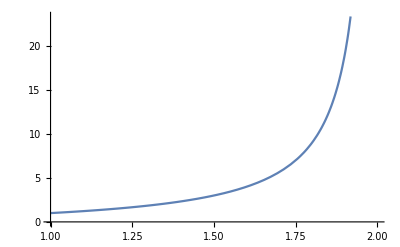

```mathematica
Plot[η/(2-η),{η,1,2}]
```

### Perturbation with Branch 1’ Expansion

```mathematica
a[r_]:=((-1+η) η)/(1+(-1+η) η)r+(2 (η-1)^2 η (3 γ-2 α (2-η) η))/((1+(η-1) η)^2 (3-(2-η) η (1+η)))1/r+ϵ h[r]
mode=1;

temp=Normal[Series[D[eqbrs,ϵ]/.ϵ->0,{r,Infinity,5}]];

Clear[a,mode]
```

```mathematica
Coefficient[temp,h''[r]]//FullSimplify
```

1

```mathematica
Series[Coefficient[temp,h'[r]],{r,Infinity,1}]//FullSimplify
```

((-1+η) ((-8+η) η+6 √(η^2)))/((-2+η) η r)+O[1/r]^2

which is equal to ‘(η-1)/r’.

```mathematica
Series[Coefficient[temp,h[r]],{r,Infinity,2}]//FullSimplify
```

(-6 γ √(η^2)+γ η (5+(3-2 η) η)+6 α (-η+√(η^2)))/(γ (-2+η) r^2)+O[1/r]^3

which is equal to ‘(2 η^3-3 η^2+η)/(r^2 (2-η))’

```mathematica
Clear[temp]
```

Then we get the 1^st-order perturbation equation: 
	h''[r]+(η-1)/r h'[r]+(2 η^3-3 η^2+η)/(r^2 (2-η))h[r]
and can be solved easily:

```mathematica
h[r_]:=r^m
Solve[r^2 h''[r]+(η-1)r h'[r]+(2 η^3-3 η^2+η)/(2-η)h[r]==0,m]//FullSimplify
Clear[h]
```

{{m→(4+(-4+η) η+√((-2+η) (-8+η (16+9 (-2+η) η))))/(4-2 η)},{m→(-4-(-4+η) η+√((-2+η) (-8+η (16+9 (-2+η) η))))/(2 (-2+η))}}

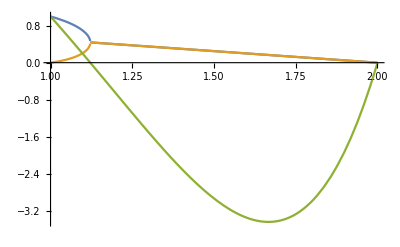

```mathematica
Plot[{Re[(4+(-4+η) η+√((-2+η) (-8+η (16+9 (-2+η) η))))/(4-2 η)],Re[(-4-(-4+η) η+√((-2+η) (-8+η (16+9 (-2+η) η))))/(2 (-2+η))],(-2+η) (-8+η (16+9 (-2+η) η))},{η,1,2}]
```

where the blue and orange lines are the real parts of m’s, and the green one is for the part inside the square root of their expression.

### Perturbation with Branch 1’’ Expansion

```mathematica
(*a[r_]:=(η^2 (3+2 (-2+η) η))/(2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2))r^3+(6 α η^4+3 γ (-3+η) (-1+η) (-3+4 η))/(2 α η^2 (-9+(-5+η) (-3+η) η)+γ (-9+η (42+η (-40+η (9+4 η)))))r+ϵ k[r]*)
a[r_]:=a3*r^3+a1*r+ϵ k[r]

mode=1;

temp=D[eqbrs,ϵ]/.ϵ->0

Clear[a,mode]
```

-(((-3 r^7 (-2+η) η^3-√3 √(r^4 (r-a1 r-a3 r^3)^4 (-2+η)^2 η^5 (16 r^2 (a1+3 a3 r^2)^2 α γ (-2+η)-24 r^4 (a1+3 a3 r^2) γ (-1+η)+3 (r^6+8 (a1 r+a3 r^3) (-r^3+2 (a1 r+a3 r^3) α) (α-γ)) η))+r^2 (-2+η) η (2 r^2 (a1+3 a3 r^2)^2 (-r+a1 r+a3 r^3) γ (-2+η)+2 r (a1+3 a3 r^2) (r-a1 r-a3 r^3) γ ((a1 r+a3 r^3) (5-4 η)+4 r (-1+η)) η+3 (a1 r+a3 r^3) (-r (a1 r+a3 r^3) (r^2+8 α-8 γ)+2 r^2 (r^2+2 α-2 γ)+4 (a1 r+a3 r^3)^2 (α-γ)) η^2)) k[r])/(r^4 (r-a1 r-a3 r^3)^3 γ (-2+η)^2 η^2))-(r^2 (-2+η) η (2 r^2 (a1+3 a3 r^2)^2 γ (-2+η) k[r]-2 r (a1+3 a3 r^2) γ ((a1 r+a3 r^3) (5-4 η)+4 r (-1+η)) η k[r]+2 r (a1+3 a3 r^2) (r-a1 r-a3 r^3) γ (5-4 η) η k[r]+3 (-r (a1 r+a3 r^3) (r^2+8 α-8 γ)+2 r^2 (r^2+2 α-2 γ)+4 (a1 r+a3 r^3)^2 (α-γ)) η^2 k[r]+3 (a1 r+a3 r^3) η^2 (-r (r^2+8 α-8 γ) k[r]+8 (a1 r+a3 r^3) (α-γ) k[r])+4 r^2 (a1+3 a3 r^2) (-r+a1 r+a3 r^3) γ (-2+η) k'[r]+2 r (r-a1 r-a3 r^3) γ ((a1 r+a3 r^3) (5-4 η)+4 r (-1+η)) η k'[r])-(√3 (-4 r^4 (r-a1 r-a3 r^3)^3 (-2+η)^2 η^5 (16 r^2 (a1+3 a3 r^2)^2 α γ (-2+η)-24 r^4 (a1+3 a3 r^2) γ (-1+η)+3 (r^6+8 (a1 r+a3 r^3) (-r^3+2 (a1 r+a3 r^3) α) (α-γ)) η) k[r]+r^4 (r-a1 r-a3 r^3)^4 (-2+η)^2 η^5 (3 η (16 (a1 r+a3 r^3) α (α-γ) k[r]+8 (-r^3+2 (a1 r+a3 r^3) α) (α-γ) k[r])+32 r^2 (a1+3 a3 r^2) α γ (-2+η) k'[r]-24 r^4 γ (-1+η) k'[r])))/(2 √(r^4 (r-a1 r-a3 r^3)^4 (-2+η)^2 η^5 (16 r^2 (a1+3 a3 r^2)^2 α γ (-2+η)-24 r^4 (a1+3 a3 r^2) γ (-1+η)+3 (r^6+8 (a1 r+a3 r^3) (-r^3+2 (a1 r+a3 r^3) α) (α-γ)) η))))/(2 r^4 (r-a1 r-a3 r^3)^2 γ (-2+η)^2 η^2)+k''[r]

```mathematica
k0Coeff=(-(-3 r^7 (-2+η) η^3-√3 √(r^4 (r-a1 r-a3 r^3)^4 (-2+η)^2 η^5 (16 r^2 (a1+3 a3 r^2)^2 α γ (-2+η)-24 r^4 (a1+3 a3 r^2) γ (-1+η)+3 (r^6+8 (a1 r+a3 r^3) (-r^3+2 (a1 r+a3 r^3) α) (α-γ)) η))+r^2 (-2+η) η (2 r^2 (a1+3 a3 r^2)^2 (-r+a1 r+a3 r^3) γ (-2+η)+2 r (a1+3 a3 r^2) (r-a1 r-a3 r^3) γ ((a1 r+a3 r^3) (5-4 η)+4 r (-1+η)) η+3 (a1 r+a3 r^3) (-r (a1 r+a3 r^3) (r^2+8 α-8 γ)+2 r^2 (r^2+2 α-2 γ)+4 (a1 r+a3 r^3)^2 (α-γ)) η^2)
)/(r^4 (r-a1 r-a3 r^3)^3 γ (-2+η)^2 η^2))-(2 r^2 (r^2 (-2+η) η)(a1+3 a3 r^2)^2 γ (-2+η)-2 r (r^2 (-2+η) η)(a1+3 a3 r^2) γ ((a1 r+a3 r^3) (5-4 η)+4 r (-1+η)) η+2 r (r^2 (-2+η) η)(a1+3 a3 r^2) (r-a1 r-a3 r^3) γ (5-4 η) η+3 (r^2 (-2+η) η)(-r (a1 r+a3 r^3) (r^2+8 α-8 γ)+2 r^2 (r^2+2 α-2 γ)+4 (a1 r+a3 r^3)^2 (α-γ)) η^2 +3 (r^2 (-2+η) η)(a1 r+a3 r^3) η^2 (-r (r^2+8 α-8 γ) +8 (a1 r+a3 r^3) (α-γ) ))/(2 r^4 (r-a1 r-a3 r^3)^2 γ (-2+η)^2 η^2)+(√3((-4 r^4 (r-a1 r-a3 r^3)^3 (-2+η)^2 η^5(16 r^2 (a1+3 a3 r^2)^2 α γ (-2+η)-24 r^4 (a1+3 a3 r^2) γ (-1+η)+3 (r^6+8 (a1 r+a3 r^3) (-r^3+2 (a1 r+a3 r^3) α) (α-γ)) η))
+(3 r^4 (r-a1 r-a3 r^3)^4 (-2+η)^2 η^6 (16 (a1 r+a3 r^3) α (α-γ)+8 (-r^3+2 (a1 r+a3 r^3) α) (α-γ) )))/((2 r^4 (r-a1 r-a3 r^3)^2 γ (-2+η)^2 η^2)(4 r^4 (r-a1 r-a3 r^3)^4 (-2+η)^2 η^5 (16 r^2 (a1+3 a3 r^2)^2 α γ (-2+η)-24 r^4 (a1+3 a3 r^2) γ (-1+η)+3 (r^6+8 (a1 r+a3 r^3) (-r^3+2 (a1 r+a3 r^3) α) (α-γ)) η))^(1/2)));
```

```mathematica
k1Coeff=(√3(r^4 (r-a1 r-a3 r^3)^4 (-2+η)^2 η^5(32 r^2 (a1+3 a3 r^2) α γ (-2+η)-24 r^4 γ (-1+η)))/((2 r^4 (r-a1 r-a3 r^3)^2 γ (-2+η)^2 η^2)(4 r^4 (r-a1 r-a3 r^3)^4 (-2+η)^2 η^5 (16 r^2 (a1+3 a3 r^2)^2 α γ (-2+η)-24 r^4 (a1+3 a3 r^2) γ (-1+η)+3 (r^6+8 (a1 r+a3 r^3) (-r^3+2 (a1 r+a3 r^3) α) (α-γ)) η))^(1/2)))-((4 r^2 (r^2 (-2+η) η)(a1+3 a3 r^2) (-r+a1 r+a3 r^3) γ (-2+η) +2 r (r^2 (-2+η) η)(r-a1 r-a3 r^3) γ ((a1 r+a3 r^3) (5-4 η)+4 r (-1+η)) η)/(2 r^4 (r-a1 r-a3 r^3)^2 γ (-2+η)^2 η^2));
```

```mathematica
k0Coeff-Coefficient[temp,k[r]]//FullSimplify
```

0

```mathematica
k1Coeff-Coefficient[temp,k'[r]]//FullSimplify
```

0

```mathematica
Series[Coefficient[temp,k''[r]],{r,Infinity,5},Assumptions->1<=η<=2&&α>0&&γ>0&&1/3<α/γ<31/18]//FullSimplify
```

1

```mathematica
Series[k1Coeff,{r,Infinity,1}]//FullSimplify
```

(-4-3/(-2+η)-6/η+(6 a3^2 (1+4 a3 α (-2+η)-η) η^3)/(√(a3^4 (-2+η)^2 η^5 (24 a3 (1-4 a3 α) γ+η+8 a3 (-1+2 a3 α) (α+2 γ) η))))/r+O[1/r]^2

```mathematica
Series[k0Coeff,{r,Infinity,2}]
```

1/r^2((3 a3 η^3 (24 a3 γ-96 a3^2 α γ+η-10 a3 α η+24 a3^2 α^2 η-14 a3 γ η+24 a3^2 α γ η))/(γ √(a3^4 (-2+η)^2 η^5 (24 a3 γ-96 a3^2 α γ+η-8 a3 α η+16 a3^2 α^2 η-16 a3 γ η+32 a3^2 α γ η)))-(3 (-6 a3 γ-7 a3 γ η-η^2+6 a3 α η^2+2 a3 γ η^2))/(a3 γ (-2+η) η)-1/(a3^3 γ (-2+η)^2 η^2)(3 √(a3^4 (-2+η)^2 η^5 (24 a3 γ-96 a3^2 α γ+η-8 a3 α η+16 a3^2 α^2 η-16 a3 γ η+32 a3^2 α γ η))-3 (-2+η) η (-12 a3^3 γ-4 a3^3 γ η-a3^2 η^2+4 a3^3 α η^2+4 a3^3 γ η^2)))+O[1/r]^3

Therefore the perturbation equation should be of form 
	k''[r]+c1*1/r k'[r]+c0*1/r^2 k[r]=0
where
	c1=-4-3/(-2+η)-6/η+(6 a3^2 (1+4 a3 α (-2+η)-η) η^3)/(√(a3^4 (-2+η)^2 η^5 (24 a3 (1-4 a3 α) γ+η+8 a3 (-1+2 a3 α) (α+2 γ) η)))
	c0=(3 a3 η^3 (24 a3 γ-96 a3^2 α γ+η-10 a3 α η+24 a3^2 α^2 η-14 a3 γ η+24 a3^2 α γ η))/(γ √(a3^4 (-2+η)^2 η^5 (24 a3 γ-96 a3^2 α γ+η-8 a3 α η+16 a3^2 α^2 η-16 a3 γ η+32 a3^2 α γ η)))-(3 (-6 a3 γ-7 a3 γ η-η^2+6 a3 α η^2+2 a3 γ η^2))/(a3 γ (-2+η) η)-1/(a3^3 γ (-2+η)^2 η^2)(3 √(a3^4 (-2+η)^2 η^5 (24 a3 γ-96 a3^2 α γ+η-8 a3 α η+16 a3^2 α^2 η-16 a3 γ η+32 a3^2 α γ η))-3 (-2+η) η (-12 a3^3 γ-4 a3^3 γ η-a3^2 η^2+4 a3^3 α η^2+4 a3^3 γ η^2))
	a3=(η^2 (3+2 (-2+η) η))/(2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2))
	a1=(6 α η^4+3 γ (-3+η) (-1+η) (-3+4 η))/(2 α η^2 (-9+(-5+η) (-3+η) η)+γ (-9+η (42+η (-40+η (9+4 η)))))

Also, this can be solved easily:

```mathematica
k[r_]:=r^m

Solve[(k''[r]+c1*1/r k'[r]+c0*1/r^2 k[r])/(r^-2*k[r])==0,m]

Clear[k]
```

{{m→1/2 (1-c1-√(1-4 c0-2 c1+c1^2))},{m→1/2 (1-c1+√(1-4 c0-2 c1+c1^2))}}

Now we examine the stability of bases.

```mathematica
c1=-4-3/(-2+η)-6/η+(6 a3^2 (1+4 a3 α (-2+η)-η) η^3)/(√(a3^4 (-2+η)^2 η^5 (24 a3 (1-4 a3 α) γ+η+8 a3 (-1+2 a3 α) (α+2 γ) η)));
c0=(3 a3 η^3 (24 a3 γ-96 a3^2 α γ+η-10 a3 α η+24 a3^2 α^2 η-14 a3 γ η+24 a3^2 α γ η))/(γ √(a3^4 (-2+η)^2 η^5 (24 a3 γ-96 a3^2 α γ+η-8 a3 α η+16 a3^2 α^2 η-16 a3 γ η+32 a3^2 α γ η)))-(3 (-6 a3 γ-7 a3 γ η-η^2+6 a3 α η^2+2 a3 γ η^2))/(a3 γ (-2+η) η)-1/(a3^3 γ (-2+η)^2 η^2)(3 √(a3^4 (-2+η)^2 η^5 (24 a3 γ-96 a3^2 α γ+η-8 a3 α η+16 a3^2 α^2 η-16 a3 γ η+32 a3^2 α γ η))-3 (-2+η) η (-12 a3^3 γ-4 a3^3 γ η-a3^2 η^2+4 a3^3 α η^2+4 a3^3 γ η^2));
a3=(η^2 (3+2 (-2+η) η))/(2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2));
a1=(6 α η^4+3 γ (-3+η) (-1+η) (-3+4 η))/(2 α η^2 (-9+(-5+η) (-3+η) η)+γ (-9+η (42+η (-40+η (9+4 η)))));
```

```mathematica
c1//Simplify
```

-4-3/(-2+η)-6/η+(6 η^7 (3-4 η+2 η^2)^2 (γ (-3+η)^2 (-1+η)+2 α η^2 (-3+4 η-3 η^2+η^3)))/((-3+η)^3 (-γ (-3+η)+2 α (-1+η) η^2)^3 √(((-2+η)^2 η^14 (3-4 η+2 η^2)^4 (2 α η^4+γ (-9+24 η-19 η^2+4 η^3))^2)/((-3+η)^6 (γ (-3+η)-2 α (-1+η) η^2)^6)))

```mathematica
c1=-4-3/(-2+η)-6/η+(6 η^7 (3-4 η+2 η^2)^2 (γ (-3+η)^2 (-1+η)+2 α η^2 (-3+4 η-3 η^2+η^3)))/((-3+η)^3 (-γ (-3+η)+2 α (-1+η) η^2)^3 ((2-η) η^7 (3-4 η+2 η^2)^2 (2 α η^4+γ (-9+24 η-19 η^2+4 η^3)))/((3-η)^3 (-γ (-3+η)+2 α (-1+η) η^2)^3))/.{α->s*γ}//FullSimplify
```

(-108+η (243+η (-126+η (-71+2 (39-8 η) η+2 s (-3+2 η) (6+(-8+η) η)))))/((-2+η) η (-9+η (24+η (-19+2 η (2+s η)))))

```mathematica
c0//Simplify
```

(2 (-1/(2 (-2+η))3 (-3+η) η^8 (3-4 η+2 η^2)^2 (-γ (-3+η)+2 α (-1+η) η^2) (2 α η (3-4 η+4 η^2)+γ (-9+24 η-22 η^2+4 η^3))-(3 η^14 (3-4 η+2 η^2)^4 (-2 α^2 η^6 (3-4 η+4 η^2)-γ^2 (-3+η)^2 (9-42 η+70 η^2-52 η^3+14 η^4)+α γ η^2 (-27+54 η-9 η^2-80 η^3+80 η^4-24 η^5+4 η^6)))/((-3+η)^2 (γ (-3+η)-2 α (-1+η) η^2)^2 √(((-2+η)^2 η^14 (3-4 η+2 η^2)^4 (2 α η^4+γ (-9+24 η-19 η^2+4 η^3))^2)/((-3+η)^6 (γ (-3+η)-2 α (-1+η) η^2)^6)))-1/(-2+η)^2 3 (3-η) (γ (-3+η)-2 α (-1+η) η^2) ((3-η)^3 (γ (-3+η)-2 α (-1+η) η^2)^3 √(((-2+η)^2 η^14 (3-4 η+2 η^2)^4 (2 α η^4+γ (-9+24 η-19 η^2+4 η^3))^2)/((-3+η)^6 (γ (-3+η)-2 α (-1+η) η^2)^6))+(2-η) η^7 (3-4 η+2 η^2)^2 (2 α η^4+γ (-9+12 η+3 η^2-12 η^3+4 η^4)))))/(γ (-3+η) η^8 (3+2 (-2+η) η)^3 (-γ (-3+η)+2 α (-1+η) η^2))

```mathematica
c0=(2 (-1/(2 (-2+η))3 (-3+η) η^8 (3-4 η+2 η^2)^2 (-γ (-3+η)+2 α (-1+η) η^2) (2 α η (3-4 η+4 η^2)+γ (-9+24 η-22 η^2+4 η^3))-(3 η^14 (3-4 η+2 η^2)^4 (-2 α^2 η^6 (3-4 η+4 η^2)-γ^2 (-3+η)^2 (9-42 η+70 η^2-52 η^3+14 η^4)+α γ η^2 (-27+54 η-9 η^2-80 η^3+80 η^4-24 η^5+4 η^6)))/((-3+η)^2 (γ (-3+η)-2 α (-1+η) η^2)^2 ((2-η) η^7 (3-4 η+2 η^2)^2 (2 α η^4+γ (-9+24 η-19 η^2+4 η^3)))/((3-η)^3 (-γ (-3+η)+2 α (-1+η) η^2)^3))-1/(-2+η)^2 3 (3-η) (γ (-3+η)-2 α (-1+η) η^2) ((3-η)^3 (γ (-3+η)-2 α (-1+η) η^2)^3 ((2-η) η^7 (3-4 η+2 η^2)^2 (2 α η^4+γ (-9+24 η-19 η^2+4 η^3)))/((3-η)^3 (-γ (-3+η)+2 α (-1+η) η^2)^3)+(2-η) η^7 (3-4 η+2 η^2)^2 (2 α η^4+γ (-9+12 η+3 η^2-12 η^3+4 η^4)))))/(γ (-3+η) η^8 (3+2 (-2+η) η)^3 (-γ (-3+η)+2 α (-1+η) η^2))/.{α->s*γ}//FullSimplify
```

(162+3 η (-171+6 (25+6 s) η-3 (7+20 s) η^2+28 (-1+s) η^3-2 (-4+s) η^4))/((-2+η) η (-9+η (24+η (-19+2 η (2+s η)))))

Then 2 m’s are

```mathematica
m1=1/2 (1-c1-√(1-4 c0-2 c1+c1^2))//Simplify
```

1/2 (1-√((11664-60264 η+139401 η^2-191862 η^3+9 (19343+648 s) η^4-12 (8999+2214 s) η^5+(45751+50292 s+1296 s^2) η^6-6 (2145+8864 s+576 s^2) η^7+(2329+34160 s+3888 s^2) η^8-8 (33+1673 s+282 s^2) η^9+4 (4+733 s+169 s^2) η^10-8 s (34+11 s) η^11+4 s^2 η^12)/((-2+η)^2 η^2 (-9+24 η-19 η^2+4 η^3+2 s η^4)^2))-(-108+η (243+η (-126+η (-71+2 (39-8 η) η+2 s (-3+2 η) (6+(-8+η) η)))))/((-2+η) η (-9+η (24+η (-19+2 η (2+s η))))))

```mathematica
m2=1/2 (1-c1+√(1-4 c0-2 c1+c1^2))//FullSimplify
```

1/2 (1+(108+η (-243+η (126+η (71+2 η (-39+8 η)-2 s (-3+2 η) (6+(-8+η) η)))))/((-2+η) η (-9+η (24+η (-19+2 η (2+s η)))))+√((11664+η (-60264+η (139401+η (-191862+η (174087+4 s^2 η^2 (-18+(-8+η) (-3+η) η)^2+η (-107988+η (45751+η (-12870+η (2329+8 η (-33+2 η)))))-4 s (-3+η) (486+η (-2052+η (3507+η (-3263+η (1759+η (-529+68 η)))))))))))/((-2+η)^2 η^2 (-9+η (24+η (-19+2 η (2+s η))))^2)))

```mathematica
mSqrt=1/2 √(1-4 c0-2 c1+c1^2);
mNormal=1/2(1-c1);
```

```mathematica
Plot3D[{Re[mNormal+mSqrt],0},{s,1/3,31/18},{η,1,1.9},PlotRange->All]
```

```mathematica
Plot3D[{Re[mNormal-mSqrt],0},{s,1/3,31/18},{η,1,1.9},PlotRange->All]
```

```mathematica
Plot3D[{Re[mNormal+mSqrt],Re[mNormal-mSqrt],0},{s,1/3,31/18},{η,1,1.9},PlotRange->All]
```

When we are in 
(1) the green parameter space, this solution is stable!
(2) the blue parameter space, this solution is unstable!
(3) the yellow parameter space, this solution acquires stability through 1-parameter tuning!

```mathematica
Clear[a3,a1,c1,c3,m1,m2,mSqrt,mNormal,k1Coeff,k0Coeff,temp]
```

### Perturbation with Branch 2 Expansion

```mathematica
a[r_]:=r-(2 γ)/(3 r η^2)+(4 γ (-6 α η^2+γ (-2+6 η+η^2)))/(9 r^3 η^4)+ϵ g[r]
mode=2;

temp=Normal[Series[D[eqbrs,ϵ]/.ϵ->0,{r,Infinity,3}]]//Simplify

Clear[a,mode]
```

1/(6 r^3 γ^2 (-2+η) η^3 √(η^2))(-3 r (9 r^4 η^6 √(η^2)+432 α^2 η^6 √(η^2)+3 r^2 γ η^4 √(η^2) (-4+23 η+4 η^2)+2 γ^2 (-171 η^3 √(η^2)+188 η^4 √(η^2)+6 η^6 √(η^2)+34 (η^2)^(3/2)+η^5 (-6+73 √(η^2)))-12 α η^4 (6 r^2 (η^2)^(3/2)+γ √(η^2) (-29+12 η^2)+γ η (-1+73 √(η^2)))) g[r]+γ ((9 (r^4-4 r^2 α+16 α^2) (-4+η) η^4 √(η^2)+4 γ^2 (156 η √(η^2)+η^5 √(η^2)-8 √(η^2) (4+21 η^2)+4 η^4 (9+2 √(η^2))-4 η^3 (9+5 √(η^2)))+6 γ (r^2 (-19 η^3 √(η^2)+4 (η^2)^(3/2)+η^5 (-6+√(η^2))-2 η^4 (-3+√(η^2)))-8 α (-28 η^3 √(η^2)+12 (η^2)^(3/2)+η^5 (2+√(η^2))+η^4 (-1+2 √(η^2))))) g'[r]+6 r^3 γ (-2+η) η^3 √(η^2) g''[r]))

```mathematica
Series[Coefficient[temp,g''[r]],{r,Infinity,0}]//FullSimplify
```

1+O[1/r]^1

```mathematica
Series[Coefficient[temp,g'[r]],{r,Infinity,0}]//FullSimplify
```

(3 (-4+η) η r)/(2 γ (-2+η))+O[1/r]^1

```mathematica
Series[Coefficient[temp,g[r]],{r,Infinity,0}]//FullSimplify
```

-(9 η^3 r^2)/(2 (γ^2 (-2+η)))+(72 α η^3-3 γ η (-4+η (23+4 η)))/(2 γ^2 (-2+η))+O[1/r]^1

```mathematica
Clear[temp]
```

Then we get the 1^st-order perturbation equation:
	g''[r]+(3 (4 - η) η r)/(2 γ (2-η)) g'[r]+(9 η^3 r^2)/(2 γ^2 (2-η))g[r]=0 ,
which can be solved as follows.

```mathematica
g[r_]:=g1[r^2]
g''[r]+(3 (4 - η) η r)/(2 γ (2-η)) g'[r]+(9 η^3 r^2)/(2 γ^2 (2-η))g[r]//FullSimplify
```

(-9 r^2 η^3 g1[r^2]+2 γ ((2 γ (-2+η)+3 r^2 (-4+η) η) g1'[r^2]+4 r^2 γ (-2+η) g1''[r^2]))/(2 γ^2 (-2+η))

which has leading behaviors: 
	(-9 r^2 η^3 g1[r^2]+2 γ ((3 r^2 (-4+η) η) g1'[r^2]+4 r^2 γ (-2+η) g1''[r^2]))/(2 γ^2 (-2+η))
and can be solved with basis

```mathematica
g1[t_]:=ⅇ^(-s t)

Solve[(-9 r^2 η^3 g1[r^2]+2 γ ((3 r^2 (-4+η) η) g1'[r^2]+4 r^2 γ (-2+η) g1''[r^2]))/(2 γ^2 (-2+η))==0,s]//FullSimplify
Clear[g,g1]
```

{{s→(3 η)/(2 γ)},{s→(3 η^2)/(8 γ-4 γ η)}}

## Setup for Static Solutions with β

```mathematica
Clear[coord,dim,metricsign,metric,im,Ein,RS,RT,Rie,WT,GTr,GUD,RT2,Rie2,WT2,G,eq,eos,A,B,psi1,psi2,psi3,psi4,eqa,eqaBrs,factor,normal,sqrt,eqbrs]
```

### Setup

```mathematica
coord={u,r,θ,ϕ};
dim=4;
metricsign=-1;
metric={{-ⅇ^A[r]/B[r],-ⅇ^(A[r]/2),0,0},{-ⅇ^(A[r]/2),0,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
im=Inverse[metric];
```

```mathematica
SetDirectory["C:\\Program Files\\Wolfram Research\\Mathematica\\12.3"]
<<diffgeo.m
```

C:\Program Files\Wolfram Research\Mathematica\12.3

```mathematica
Ein=Einstein;
RS=RicciScalar;
RT=RicciTensor;
Rie=Riemann;
WT=Weyl;
```

```mathematica
GTr=Sum[im[[i,j]] Einstein[[i,j]],{i,1,dim},{j,1,dim}];
GUD=Table[Sum[im[[i,k]] Einstein[[k,j]],{k,1,dim}],{i,1,dim},{j,1,dim}];
RT2=Sum[RT[[i,j]]RT[[a,b]]im[[i,a]]im[[j,b]],{i,1,dim},{j,1,dim},{a,1,dim},{b,1,dim}];
Rie2=Sum[Rie[[i,j,k,l]] Rie[[a,b,c,d]] im[[i,a]]im[[j,b]]im[[k,c]]metric[[l,d]],{i,1,dim},{j,1,dim},{k,1,dim},{l,1,dim},{a,1,dim},{b,1,dim},{c,1,dim},{d,1,dim}];
WT2=Sum[WT[[i,j,k,l]]WT[[a,b,c,d]]im[[i,a]]im[[j,b]]im[[k,c]]im[[l,d]],{i,1,dim},{j,1,dim},{k,1,dim},{l,1,dim},{a,1,dim},{b,1,dim},{c,1,dim},{d,1,dim}];
G=Rie2-4 RT2+RS^2;
BoxR=scalarLaplacian[RS];
```

The semi-classical Einstein equation is:

```mathematica
eq=GTr-(γ WT2-α G+β BoxR);
```

Also for later convenience, the equation of state is given by ‘EoS’ to 0:

```mathematica
eos=(-GUD[[2,2]])/GUD[[1,1]]-(2-η)/η;
```

```mathematica
A[r_]:=2ψ[r] (* ψ[u_,r_]:=-(∫_r)^R0[u]((∂_ρ a[u,ρ])/(ρ-a[u,ρ]))ⅆρ *)
B[r_]:=(1-a[r]/r)^-1
```

```mathematica
psi1=D[a[r], r]/(η(r-a[r]));
psi2=D[psi1,r];
psi3=D[psi2,r];
psi4=D[psi3,r];
```

```mathematica
eqaBeta=eq/.{Derivative[1][ψ][r]->psi1,Derivative[2][ψ][r]->psi2,Derivative[3][ψ][r]->psi3,Derivative[4][ψ][r]->psi4}//FullSimplify
```

1/(3 r^6 η^4 (r-a[r])^2)(36 (α-γ) η^4 a[r]^4+3 r η^3 a[r]^3 (24 (-α+γ) η-4 (β+5 γ-2 (β+2 γ) η+α (-5+4 η)) a'[r]+r (β+8 γ+4 α (-2+η)-5 β η-4 γ η) a''[r]+r^2 β ((1+η) a^(3)[r]+r (-2+η) a^(4)[r]))+r^4 (η (8 γ (-2+η) (-1+η)+3 β (1+η) (-4+3 η)) a'[r]^3-(-2+η) (γ (-2+η)+3 β η (1+η)) a'[r]^4+η a'[r]^2 (η (-3 r^2 (-2+η)-16 γ (-1+η)^2+6 η (β+2 α (-2+η)-2 β η))-r (-2+η) (2 γ (-2+η)+β (6+9 η)) a''[r])+η^2 a'[r] (-6 (r^2+2 β) (-1+η) η+r (8 γ (-2+η) (-1+η)+3 β (-8+η (6+η))) a''[r]+3 r^2 β (-3+η) (-2+η) a^(3)[r])-r η^2 (3 (r^2 (-2+η)-4 β (-1+η)) η a''[r]+r (6 β+γ (-2+η)) (-2+η) a''[r]^2+3 r β η (2 (-1+η) a^(3)[r]+r (-2+η) a^(4)[r])))+r^2 η^2 a[r]^2 (36 (α-γ) η^2+(12 α (-2+η) (-1+η)+3 β (5-4 η) η+γ (-49+4 (13-4 η) η)) a'[r]^2+a'[r] (3 η (r^2-36 α+11 β+36 γ-2 (r^2-16 α+10 β+16 γ) η)+r (2 γ (-2+η) (-5+4 η)+3 β (-5+η (2+η))) a''[r]+3 r^2 β (-3+η) (-2+η) a^(3)[r])+r (-3 η (5 β+16 γ+r^2 (-2+η)+8 α (-2+η)-14 β η-8 γ η) a''[r]-r (6 β+γ (-2+η)) (-2+η) a''[r]^2-3 r β η (4 η a^(3)[r]+3 r (-2+η) a^(4)[r])))+r^3 η a[r] (-((-2+η) (3 β+2 γ (-5+4 η)) a'[r]^3)+a'[r]^2 (η (-24 α+3 β+64 γ+3 r^2 (-2+η)+2 η (6 α (5-2 η)+3 β (-5+4 η)+2 γ (-21+8 η)))+r (-2+η) (2 γ (-2+η)+β (6+9 η)) a''[r])-η a'[r] (3 r^2 (3-4 η) η+6 η (5 β+8 γ+8 α (-1+η)-8 (β+γ) η)+r (-39 β+6 β η (4+η)+2 γ (-2+η) (-9+8 η)) a''[r]+6 r^2 β (-3+η) (-2+η) a^(3)[r])+r η (3 η (-8 α+8 (β+γ)+2 r^2 (-2+η)+4 α η-13 β η-4 γ η) a''[r]+2 r (6 β+γ (-2+η)) (-2+η) a''[r]^2+3 r β η ((-3+5 η) a^(3)[r]+3 r (-2+η) a^(4)[r]))))

### Perturbation with Branch 1 Expansion

```mathematica
a[r_]:=a0+(2 a0^2 (γ-α) η)/(3-η)1/r^3+(3 a0^3 (γ-α) η)/(2 (3-η) (8-3 η))1/r^4+ϵ f[r]

temp=Normal[Series[D[eqaBeta,ϵ]/.ϵ->0,{r,Infinity,2}]]//Simplify

Clear[a]
```

1/(r^2 η)(-2 (-1+η) f'[r]-r (-2+η) f''[r]-2 β (-1+η) f^(3)[r]+(a0-r) β (-2+η) f^(4)[r])

where the coefficients are (normalize that of f’’’’[r] to 1)

```mathematica
Coefficient[temp,f'''[r]]/Coefficient[temp,f''''[r]]//FullSimplify
```

-(2 (-1+η))/((a0-r) (-2+η))

```mathematica
Coefficient[temp,f''[r]]/Coefficient[temp,f''''[r]]//FullSimplify
```

r/((-a0+r) β)

```mathematica
Coefficient[temp,f'[r]]/Coefficient[temp,f''''[r]]//FullSimplify
```

-(2 (-1+η))/((a0-r) β (-2+η))

```mathematica
Clear[temp]
```

Then we get the perturbation equation at large r as
	f''''[r]-(2 (η-1))/(r (2-η))f'''[r]+1/β f''[r]-(2 (η-1))/((r-a0) β (2-η))f'[r]=0
and can be solved as follows: 
	((∂_r)^3-(2 (η-1))/(r (2-η))(∂_r)^2+1/β∂_r -(2 (η-1))/(r β (2-η)))∂_r f[r]
=(∂_r ((∂_r)^2+1/β)-(2 (η-1))/(r (2-η))((∂_r)^2+1/β))∂_r f[r]
=(∂_r -(2 (η-1))/(r (2-η)))((∂_r)^2+1/β)∂_r f[r]
=(∂_r -(2 (η-1))/(r (2-η)))∂_r ((∂_r)^2+1/β)f[r]
Then we can solve it from the left:

```mathematica
DSolve[D[f1[r], r]-(2 (η-1))/(r (2-η))f1[r]==0,f1[r],r]//FullSimplify
```

{{f1[r]→r^(-2-2/(-2+η)) C[1]}}

```mathematica
DSolve[D[f2[r], r]==r^(-2-2/(-2+η)) C[1],f2[r],r]//FullSimplify
```

{{f2[r]→-(r^(-η/(-2+η)) (-2+η) C[1])/η+C[2]}}

```mathematica
DSolve[D[f3[r], r,r]+1/β f3[r]==-(r^(-η/(-2+η)) (-2+η) C[1])/η+C[2],f3[r],r]//FullSimplify
```

{{f3[r]→β C[2]+C[3] Cos[r/(√β)]+1/(2 η)ⅈ ⅇ^(-(ⅈ r)/(√β)) r^(-2/(-2+η)) √β (-2+η) C[1] (ExpIntegralE[η/(-2+η),-(ⅈ r)/(√β)]-ⅇ^((2 ⅈ r)/(√β)) ExpIntegralE[η/(-2+η),(ⅈ r)/(√β)])+C[4] Sin[r/(√β)]}}

```mathematica
Series[1/(2 η)ⅈ ⅇ^(-(ⅈ r)/(√β)) r^(-2/(-2+η)) √β (-2+η) C[1] (ExpIntegralE[η/(-2+η),-(ⅈ r)/(√β)]-ⅇ^((2 ⅈ r)/(√β)) ExpIntegralE[η/(-2+η),(ⅈ r)/(√β)]),{r,Infinity,1}]//FullSimplify
```

r^(-2/(-2+η)) (-(β (-2+η) C[1])/(η r)+O[1/r]^2)

The power of r is -2/(-2+η)-1=η/(2-η), which is always non-negative, i.e., unstable mode.

Therefore the perturbation solution space is given by the span of {1,r^(η/(2-η)),Cos[r/(√β)], Sin[r/(√β)]}.

### Perturbation with Branch 1’ Expansion

```mathematica
a[r_]:=((-1+η) η)/(1+(-1+η) η)r+(2 (η-1)^2 η (3 γ-2 α (2-η) η))/((1+(η-1) η)^2 (3-(2-η) η (1+η)))1/r+ϵ h[r]

temp=Normal[Series[D[eqaBeta,ϵ]/.ϵ->0,{r,Infinity,3}]]//FullSimplify

Clear[a]
```

(η (1+(-1+η) η)^2 (3+η (-11+11 η-5 η^3+2 η^4)) h[r]-r (-2+η) (-1+η) (1+(-1+η) η)^2 (3+(-2+η) η (1+η)) h'[r]+6 r^2 h''[r]+24 β h''[r]-24 γ h''[r]-19 r^2 η h''[r]+24 α η h''[r]-79 β η h''[r]+76 γ η h''[r]+32 r^2 η^2 h''[r]-76 α η^2 h''[r]+109 β η^2 h''[r]-104 γ η^2 h''[r]-30 r^2 η^3 h''[r]+104 α η^3 h''[r]-69 β η^3 h''[r]+68 γ η^3 h''[r]+13 r^2 η^4 h''[r]-68 α η^4 h''[r]-5 β η^4 h''[r]+4 r^2 η^5 h''[r]+38 β η^5 h''[r]-32 γ η^5 h''[r]-9 r^2 η^6 h''[r]+32 α η^6 h''[r]-21 β η^6 h''[r]+20 γ η^6 h''[r]+5 r^2 η^7 h''[r]-20 α η^7 h''[r]+2 β η^7 h''[r]-4 γ η^7 h''[r]-r^2 η^8 h''[r]+4 α η^8 h''[r]+β η^8 h''[r]-12 r β h^(3)[r]+38 r β η h^(3)[r]-52 r β η^2 h^(3)[r]+34 r β η^3 h^(3)[r]-16 r β η^5 h^(3)[r]+10 r β η^6 h^(3)[r]-2 r β η^7 h^(3)[r]-β (-2+η) (-2 (-1+η)^2 η (3 γ+2 α (-2+η) η)+r^2 (3+η (-5+4 η-2 η^3+η^4))) h^(4)[r])/(r^3 η (1+(-1+η) η)^2 (3+(-2+η) η (1+η)))

```mathematica
Series[Coefficient[temp,h'''[r]]/Coefficient[temp,h''''[r]],{r,Infinity,1}]//FullSimplify
```

(2 (-1+η))/r+O[1/r]^2

```mathematica
Series[Coefficient[temp,h''[r]]/Coefficient[temp,h''''[r]],{r,Infinity,1}]//FullSimplify
```

(1+(-1+η) η)/β+O[1/r]^2

```mathematica
Series[Coefficient[temp,h'[r]]/Coefficient[temp,h''''[r]],{r,Infinity,1}]//FullSimplify
```

((-1+η) (1+(-1+η) η))/(β r)+O[1/r]^2

```mathematica
Series[Coefficient[temp,h[r]]/Coefficient[temp,h''''[r]],{r,Infinity,2}]//FullSimplify
```

-((-1+η) η (-1+2 η) (1+(-1+η) η))/(β (-2+η) r^2)+O[1/r]^3

We get the perturbation equation: 
	h''''[r]+(2 (η-1))/r h'''[r]+(1+(-1+η) η)/β h''[r]+((η-1) (1+(-1+η) η))/(r β)h'[r]+((η-1) η (2 η-1) (1+(-1+η) η))/(β (2-η) r^2)h[r]=0

Now we consider 2 different limits: long-wavelength and short-wavelength limits: 
1. 
Long-wavelength: ∂_r ~O(1): The perturbation equation can be approximated by
	h''''[r]+(1+(-1+η) η)/β h''[r]=0,
and is solved by solutions in the space: span{1,r}x span{Sin[r √((-1+η-η^2)/β)],Cos[r √((-1+η-η^2)/β)]}.

2.
Short-wavelength: ∂_r ~1/r: The perturbation equation can be approximated by 
	(1+(-1+η) η)/β h''[r]+((η-1) (1+(-1+η) η))/(r β)h'[r]+((η-1) η (2 η-1) (1+(-1+η) η))/(β (2-η) r^2)h[r]=0
and is solve by elements in the solution space: span{r^(1/2(2-η-√(16+24/(-2+η)+9 η^2))),r^(1/2(2-η+√(16+24/(-2+η)+9 η^2)))}

```mathematica
DSolve[(1+(-1+η) η)/β h''[r]+((η-1) (1+(-1+η) η))/(r β)h'[r]+((η-1) η (2 η-1) (1+(-1+η) η))/(β (2-η) r^2)h[r]==0,h[r],r]//Expand
```

{{h[r]→r^(1-η/2-1/2 √(16+24/(-2+η)+9 η^2)) C[1]+(r^(1-η/2+1/2 √(16+24/(-2+η)+9 η^2)) C[2])/(√(16+24/(-2+η)+9 η^2))}}

```mathematica
Solve[16+24/(-2+η)+9 η^2==0,η]//N
```

{{η→1.12155},{η→0.439224-0.774361 ⅈ},{η→0.439224+0.774361 ⅈ}}

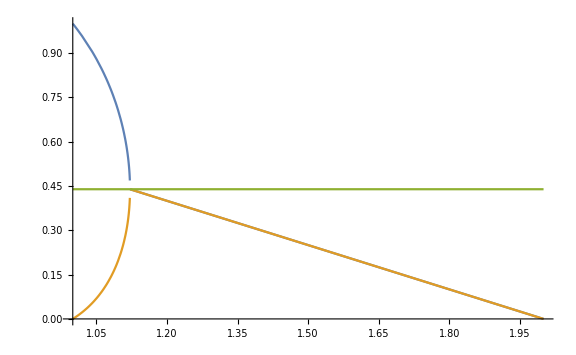

```mathematica
value=Evaluate[1/2(2-η-√(16+24/(-2+η)+9 η^2))/.η->1.1215518692186794];
Plot[{Re[1/2(2-η+√(16+24/(-2+η)+9 η^2))],Re[1/2(2-η-√(16+24/(-2+η)+9 η^2))],value},{η,1,2},ImageSize->Large]
Clear[value]
```

### Perturbation with Branch 1’’ Expansion

```mathematica
a[r_]:=a3*r^3+ϵ k[r]

temp=Normal[Series[D[eqaBeta,ϵ]/.ϵ->0,{r,Infinity,5}]];

Clear[a]
```

```mathematica
Normal[Series[Coefficient[temp,k'''[r]]/Coefficient[temp,k''''[r]],{r,Infinity,1}]]//FullSimplify
```

(2 (9+η (-7+2 η)))/(r (-2+η) η)

```mathematica
Normal[Series[Coefficient[temp,k''[r]]/Coefficient[temp,k''''[r]],{r,Infinity,2}]]//FullSimplify
```

-1/(a3 r^2 β (-2+η) η^2)((-2+η) η^2-4 a3 (-2+η) (γ (-3+η)+α η^2)+a3 β (36+η (3+2 (-5+η) η)))

```mathematica
Normal[Series[Coefficient[temp,k'[r]]/Coefficient[temp,k''''[r]],{r,Infinity,3}]]//FullSimplify
```

1/(a3 r^3 β (-2+η) η^3)(η^2 (-12+(7-2 η) η)+a3 (-4 γ (-3+η) (-12+η+4 η^2)+η (4 α η (12+η (-13+2 η))+β (126+η (-57-4 (-2+η) η)))))

```mathematica
Normal[Series[Coefficient[temp,k[r]]/Coefficient[temp,k''''[r]],{r,Infinity,4}]]//FullSimplify
```

1/(a3 r^4 β (-2+η) η^3)(-9 (-2+η) η^2+3 a3 (27 β (-2+η) η+4 α η^3+4 γ (-3+η) (-6+η (3+2 η))))

We get the perturbation equation: 
	k''''[r]+(2 (9+η (-7+2 η)))/(r (-2+η) η)k'''[r]-((-2+η) η^2-4 a3 (-2+η) (γ (-3+η)+α η^2)+a3 β (36+η (3+2 (-5+η) η)))/(a3 r^2 β (-2+η) η^2)k''[r]+(η^2 (-12+(7-2 η) η)+a3 (-4 γ (-3+η) (-12+η+4 η^2)+η (4 α η (12+η (-13+2 η))+β (126+η (-57-4 (-2+η) η)))))/(a3 r^3 β (-2+η) η^3)k'[r]+(-9 (-2+η) η^2+3 a3 (27 β (-2+η) η+4 α η^3+4 γ (-3+η) (-6+η (3+2 η))))/(a3 r^4 β (-2+η) η^3)k[r]=0
where 
	a3=(η^2 (3+2 (-2+η) η))/(2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2));
a1=(6 α η^4+3 γ (-3+η) (-1+η) (-3+4 η))/(2 α η^2 (-9+(-5+η) (-3+η) η)+γ (-9+η (42+η (-40+η (9+4 η)))));

```mathematica
k[r_]:=r^m

poly=a3 β (-2+η) η^3*(k''''[r]+(2 (9+η (-7+2 η)))/(r (-2+η) η)k'''[r]-(((-2+η) η^2-4 a3 (-2+η) (γ (-3+η)+α η^2)+a3 β (36+η (3+2 (-5+η) η)))/(a3 r^2 β (-2+η) η^2))k''[r]+((η^2 (-12+(7-2 η) η)+a3 (-4 γ (-3+η) (-12+η+4 η^2)+η (4 α η (12+η (-13+2 η))+β (126+η (-57-4 (-2+η) η)))))/(a3 r^3 β (-2+η) η^3))k'[r]+((-9 (-2+η) η^2+3 a3 (27 β (-2+η) η+4 α η^3+4 γ (-3+η) (-6+η (3+2 η))))/(a3 r^4 β (-2+η) η^3))k[r])/r^(-4+m)//Simplify

(*Solve[%==0,m]*)(*/.{a3->(η^2 (3+2 (-2+η) η))/(2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2)),a1->(6 α η^4+3 γ (-3+η) (-1+η) (-3+4 η))/(2 α η^2 (-9+(-5+η) (-3+η) η)+γ (-9+η (42+η (-40+η (9+4 η)))))}//FullSimplify*)

Clear[k]
```

-η^2 (9 (-2+η)+m^2 (-2+η) η+m (12-5 η+η^2))+a3 (4 γ (-3+η) (-18+9 η+m^2 (-2+η) η+6 η^2+m (12+η-5 η^2))+η (4 α η (3 η+m^2 (-2+η) η+m (12-11 η+η^2))+(-3+m) β (-27 (-2+η)+m^3 (-2+η) η^2+m^2 η (18-8 η+η^2)+m (-36-3 η+6 η^2))))

```mathematica
m4Coeff=2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2)*Coefficient[poly,m^4]/.{a3->(η^2 (3+2 (-2+η) η))/(2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2)),a1->(6 α η^4+3 γ (-3+η) (-1+η) (-3+4 η))/(2 α η^2 (-9+(-5+η) (-3+η) η)+γ (-9+η (42+η (-40+η (9+4 η)))))}/.{γ->1,α->Subscript[s, 1],β->Subscript[s, 2]}//FullSimplify
m3Coeff=2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2)*Coefficient[poly,m^3]/.{a3->(η^2 (3+2 (-2+η) η))/(2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2)),a1->(6 α η^4+3 γ (-3+η) (-1+η) (-3+4 η))/(2 α η^2 (-9+(-5+η) (-3+η) η)+γ (-9+η (42+η (-40+η (9+4 η)))))}/.{γ->1,α->Subscript[s, 1],β->Subscript[s, 2]}//FullSimplify
m2Coeff=2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2)*Coefficient[poly,m^2]/.{a3->(η^2 (3+2 (-2+η) η))/(2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2)),a1->(6 α η^4+3 γ (-3+η) (-1+η) (-3+4 η))/(2 α η^2 (-9+(-5+η) (-3+η) η)+γ (-9+η (42+η (-40+η (9+4 η)))))}/.{γ->1,α->Subscript[s, 1],β->Subscript[s, 2]}//FullSimplify
m1Coeff=2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2)*Coefficient[poly,m]/.{a3->(η^2 (3+2 (-2+η) η))/(2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2)),a1->(6 α η^4+3 γ (-3+η) (-1+η) (-3+4 η))/(2 α η^2 (-9+(-5+η) (-3+η) η)+γ (-9+η (42+η (-40+η (9+4 η)))))}/.{γ->1,α->Subscript[s, 1],β->Subscript[s, 2]}//FullSimplify
m0Coeff=2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2)*poly/.m->0/.{a3->(η^2 (3+2 (-2+η) η))/(2 (-3+η) (-γ (-3+η)+2 α (-1+η) η^2)),a1->(6 α η^4+3 γ (-3+η) (-1+η) (-3+4 η))/(2 α η^2 (-9+(-5+η) (-3+η) η)+γ (-9+η (42+η (-40+η (9+4 η)))))}/.{γ->1,α->Subscript[s, 1],β->Subscript[s, 2]}//FullSimplify
```

(-2+η) η^5 (3+2 (-2+η) η) s_2

-2 η^4 (3+2 (-2+η) η) (-9+η+η^2) s_2

η^3 (2 (-2+η) ((-3+η) (-1+η) (-3+4 η)+2 η^4 s_1)-3 (3+2 (-2+η) η) (12+η (19+(-10+η) η)) s_2)

2 η^2 (-((-3+η) (-1+η) (36+η (-27+5 η (-5+4 η))))+2 η^3 (-18+η (36+(-17+η) η)) s_1-9 η (3+2 (-2+η) η) (-9+η+η^2) s_2)

3 η^2 (2 (-3+η) (-18+η (51+η (-33-4 η+8 η^2)))-4 η^2 (-18+η (30+(-14+η) η)) s_1+27 (-2+η) η (3+2 (-2+η) η) s_2)

```mathematica
polym=(m4Coeff*m^4+m3Coeff*m^3+m2Coeff*m^2+m1Coeff*m+m0Coeff)

{m1,m2}={-10^4,10^4};
Manipulate[Plot[polym/.{Subscript[s, 1]->s1,Subscript[s, 2]->s2,η->eta},{m,m1,m2},PlotRange->{{m1/10,m2/10},{-10^8,10^8}}],{{s1,1},1/3,31/18},{{s2,0},-10,10},{{eta,1.2},1,2}]
```

m^4 (-2+η) η^5 (3+2 (-2+η) η) s_2-2 m^3 η^4 (3+2 (-2+η) η) (-9+η+η^2) s_2+3 η^2 (2 (-3+η) (-18+η (51+η (-33-4 η+8 η^2)))-4 η^2 (-18+η (30+(-14+η) η)) s_1+27 (-2+η) η (3+2 (-2+η) η) s_2)+2 m η^2 (-((-3+η) (-1+η) (36+η (-27+5 η (-5+4 η))))+2 η^3 (-18+η (36+(-17+η) η)) s_1-9 η (3+2 (-2+η) η) (-9+η+η^2) s_2)+m^2 η^3 (2 (-2+η) ((-3+η) (-1+η) (-3+4 η)+2 η^4 s_1)-3 (3+2 (-2+η) η) (12+η (19+(-10+η) η)) s_2)

Plot::plln: Limiting value m1 in {m,m1,m2} is not a machine-sized real number.

```mathematica
Manipulate[Solve[(polym/.{Subscript[s, 1]->s1,Subscript[s, 2]->s2,η->eta})==0,m],{{s1,1/3},1/3,31/18,0.01},{{s2,0},-10^5,10^5,0.01},{{eta,1.8},1,2,0.01}]
```

### Perturbation with Branch 2 Expansion

```mathematica
a[r_]:=r-(2 γ)/(3 r η^2)+(4 γ (-6 α η^2+γ (-2+6 η+η^2)))/(9 r^3 η^4)+ϵ g[r]

temp=Normal[Series[D[eqaBeta,ϵ]/.ϵ->0,{r,Infinity,3}]]//Simplify

Clear[a]
```

1/(6 r^3 γ^2 η^3)(-3 η (2 γ^2 (86-415 η+480 η^2+149 η^3+10 η^4)+9 η^3 (r^4 η-r^2 (β+12 α η)+8 α (-β+14 α η))+3 γ η (β (-6+23 η+4 η^2)+r^2 η (-4+35 η+4 η^2)-16 α η (-16+43 η+6 η^2))) g[r]+3 r η (9 (r^2-8 α) β η^3+2 γ^2 (4-37 η-2 η^2+η^3)+3 γ η ((r^2-8 α) (-4+η) η+β (-2+27 η+4 η^2))) g'[r]+γ (3 η (2 γ (-2+η) (4 γ+(r^2-4 α) η)+β (3 (r^2-4 α) η (4+η)+2 γ (22+8 η+η^2))) g''[r]-4 β γ (3 r (-3+η) η g^(3)[r]+γ (-2+η) g^(4)[r])))

where the coefficients at large r are (normalize that of g’’’’[r] to 1)

```mathematica
Series[Coefficient[temp,g'''[r]]/Coefficient[temp,g''''[r]],{r,Infinity,1}]//FullSimplify
```

(3 (-3+η) η r)/(γ (-2+η))+O[1/r]^2

```mathematica
Series[Coefficient[temp,g''[r]]/Coefficient[temp,g''''[r]],{r,Infinity,1}]//FullSimplify
```

-(3 (η^2 (2 γ (-2+η)+3 β (4+η))) r^2)/(4 (β γ^2 (-2+η)))-(3 (η (-6 α β η (4+η)+4 γ (-2+η) (γ-α η)+β γ (22+η (8+η)))))/(2 (β γ^2 (-2+η)))+O[1/r]^2

```mathematica
Series[Coefficient[temp,g'[r]]/Coefficient[temp,g''''[r]],{r,Infinity,1}]//FullSimplify
```

-(9 (η^3 (γ (-4+η)+3 β η)) r^3)/(4 (β γ^3 (-2+η)))+1/(4 β γ^3 (-2+η))3 η (72 α β η^3-2 γ^2 (4+η (-37+(-2+η) η))-3 γ η (-8 α (-4+η) η+β (-2+η (27+4 η)))) r+O[1/r]^2

```mathematica
Series[Coefficient[temp,g[r]]/Coefficient[temp,g''''[r]],{r,Infinity,1}]//FullSimplify
```

(27 η^5 r^4)/(4 β γ^3 (-2+η))+(9 η^3 (-3 η (β+12 α η)+γ (-4+η (35+4 η))) r^2)/(4 β γ^3 (-2+η))+1/(4 β γ^3 (-2+η))3 η (72 α η^3 (-β+14 α η)-3 γ η (-β (6+η) (-1+4 η)+16 α η (-16+η (43+6 η)))+2 γ^2 (86+η (-415+η (480+η (149+10 η)))))+O[1/r]^2

```mathematica
Clear[temp]
```

Hence at large r, the perturbation equation takes the form

```mathematica
g''''[r]+(3 (3-η) η r)/(γ (2-η))g'''[r]+(3η (3 β η (4+η)-2 γ η (2-η))r^2)/(4 β γ^2 (2-η))g''[r]+(9 η^3 (3 β η-γ (4-η))r^3)/(4 β γ^3 (2-η))g'[r]-(27 η^5 r^4)/(4 β γ^3 (2-η))g[r];
```

```mathematica
g[r_]:=g1[r^2]
g1[t_]:=ⅇ^(-s t)

Normal[Series[g''''[r]+(3 (3-η) η r)/(γ (2-η))g'''[r]+(3η (3 β η (4+η)-2 γ η (2-η))r^2)/(4 β γ^2 (2-η))g''[r]+(9 η^3 (3 β η-γ (4-η))r^3)/(4 β γ^3 (2-η))g'[r]-(27 η^5 r^4)/(4 β γ^3 (2-η))g[r],{r,Infinity,-4}]]//FullSimplify

Clear[g,g1]
```

1/(4 β γ^3 (-2+η))ⅇ^(-r^2 s) (64 r^4 s^4 β γ^3 (-2+η)-96 r^4 s^3 β γ^2 (-3+η) η+27 r^4 η^5+18 r^4 s η^3 (γ (-4+η)+3 β η)+12 s^2 γ (4 β γ^2 (-2+η)-2 r^4 γ (-2+η) η^2-3 r^4 β η^2 (4+η)))

```mathematica
Series[64 r^4 s^4 β γ^3 (-2+η)+27 r^4 η^5-96 r^2 s^3 β γ^2 (2 γ (-2+η)+r^2 (-3+η) η)+6 r^2 s η^2 (2 γ^2 (-2+η)+3 r^2 γ (-4+η) η+9 r^2 β η^2+3 β γ (4+η))+12 s^2 γ (-2 r^4 γ (-2+η) η^2+β (4 γ^2 (-2+η)+12 r^2 γ (-3+η) η-3 r^4 η^2 (4+η))),{r,Infinity,1}]//FullSimplify
```

(2 s γ-3 η) (8 s^2 β γ-6 s β η-3 η^2) (4 s γ (-2+η)+3 η^2) r^4+6 s γ (-32 s^2 β γ^2 (-2+η)+24 s β γ (-3+η) η+η^2 (2 γ (-2+η)+3 β (4+η))) r^2+48 s^2 β γ^3 (-2+η)+O[1/r]^2

```mathematica
Solve[(2 s γ-3 η) (8 s^2 β γ-6 s β η-3 η^2) (4 s γ (-2+η)+3 η^2)==0,s]//FullSimplify
```

{{s→(3 η)/(2 γ)},{s→(3 η^2)/(8 γ-4 γ η)},{s→(3 β η-√3 √(β (3 β+8 γ) η^2))/(8 β γ)},{s→(3 β η+√3 √(β (3 β+8 γ) η^2))/(8 β γ)}}